```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,4}]//tf
Select[nCollatz[33],OddQ]
nFaulhaber[2,4]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64

{33,25,19,29,11,17,13,5,1}

30

## Queue MMa.SE Questions

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

### Q.1

```mathematica
DirichletConvolve[1,u[n],n,m]//FullForm
```

DivisorSum[m,Function[u[Slot[1]]]]

### Q.2

```mathematica
DirichletTransform[Abs[MoebiusMu[n]],n,s]
```

Zeta[s]/Zeta[2 s]

```mathematica
DirichletTransform[MoebiusMu[n]^2,n,s]
```

DirichletTransform[MoebiusMu[n]^2,n,s]

```mathematica
Table[{k,Abs[MoebiusMu[k]],MoebiusMu[k]^2},{k,1,6}]//tf
```

1 | 1 | 1
2 | 1 | 1
3 | 1 | 1
4 | 0 | 0
5 | 1 | 1
6 | 1 | 1

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes ANT

*Foundations

## Equivalence Relation

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,1,101}]
```

{{1,0},{2,-1},{3,1},{4,-1/2},{5,1/2},{6,-1/3},{7,1/3},{8,-2},{9,2},{10,-1/5},{11,1/5},{12,-1/6},{13,1/6},{14,-1/7},{15,1/7},{16,-1/4},{17,1/4},{18,-3},{19,3},{20,-1/10},{21,1/10},{22,-1/11},{23,1/11},{24,-2/3},{25,2/3},{26,-1/13},{27,1/13},{28,-1/14},{29,1/14},{30,-1/15},{31,1/15},{32,-4},{33,4},{34,-1/17},{35,1/17},{36,-3/2},{37,3/2},{38,-1/19},{39,1/19},{40,-2/5},{41,2/5},{42,-1/21},{43,1/21},{44,-1/22},{45,1/22},{46,-1/23},{47,1/23},{48,-1/12},{49,1/12},{50,-5},{51,5},{52,-1/26},{53,1/26},{54,-1/9},{55,1/9},{56,-2/7},{57,2/7},{58,-1/29},{59,1/29},{60,-1/30},{61,1/30},{62,-1/31},{63,1/31},{64,-1/8},{65,1/8},{66,-1/33},{67,1/33},{68,-1/34},{69,1/34},{70,-1/35},{71,1/35},{72,-6},{73,6},{74,-1/37},{75,1/37},{76,-1/38},{77,1/38},{78,-1/39},{79,1/39},{80,-1/20},{81,1/20},{82,-1/41},{83,1/41},{84,-1/42},{85,1/42},{86,-1/43},{87,1/43},{88,-2/11},{89,2/11},{90,-3/5},{91,3/5},{92,-1/46},{93,1/46},{94,-1/47},{95,1/47},{96,-4/3},{97,4/3},{98,-7},{99,7},{100,-5/2},{101,5/2}}

```mathematica
nQuotientToNatural[66/71]
nQuotientToNatural[70/71]
nQuotientToNatural[(2 5 11)/(3 7 13)]
```

618553

695801

6606601

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,6606600,6606605}]
```

{{6606600,-110/273},{6606601,110/273},{6606602,-1/3303301},{6606603,1/3303301},{6606604,-1/3303302},{6606605,1/3303302}}

*Numerical Methods and Tools

## d^k/n

### d^2/n

The subset of the divisors of n for which the square is also a divisor of n. { d^2/n | d / n ∧ d^2/n } = ∏_i p_i^⌊α_i/2⌋

#### Example

```mathematica
nDivisors[36,1]
nDivisors[36,2]
nDivisors[36,3]
```

{1,2,3,4,6,9,12,18,36}

{1,2,3,6}

{1}

## Double Sums

```mathematica
Sum[j^2,{k,1,6},{j,1,k}]
Sum[k^2(6-k+1),{k,1,6}]
```

196

196

```mathematica
Sum[j,{k,1,3},{j,1,k}]
```

## Bernoulli Polynomials

### Definition / Theorem

#### Overview of Bernoulli Polynomials 1 to 8

```mathematica
Table[{k,BernoulliB[k,x]},{k,1,8}]//tf
```

1 | -1/2+x
2 | 1/6-x+x^2
3 | x/2-(3 x^2)/2+x^3
4 | -1/30+x^2-2 x^3+x^4
5 | -x/6+(5 x^3)/3-(5 x^4)/2+x^5
6 | 1/42-x^2/2+(5 x^4)/2-3 x^5+x^6
7 | x/6-(7 x^3)/6+(7 x^5)/2-(7 x^6)/2+x^7
8 | -1/30+(2 x^2)/3-(7 x^4)/3+(14 x^6)/3-4 x^7+x^8

#### Example

```mathematica
Manipulate[
Column[{Plot[BernoulliB[k,x],{x,0,1}],BernoulliB[k,x],BernoulliB[k]}],{k,1,8,1}]
```

## Abel Summation / Partial Summation

### Definition

∑_(y<n⩽x) a(n) f(n) = A(x) f(x)-A(y)f(y)-∫_y^x A(t)f'(t)ⅆt

#### Example

## Euler’s Summation Formula

### Definition

∑_(y<n⩽x) f(n) = ∫_y^x f(t)ⅆt +∫_y^x (t-[t])f'(t)ⅆt+ f(x)([x]-x)-f(y)([y]-y)

∑_(1<n⩽x) f(n) = ∫_1^x f(t)ⅆt +∫_1^x (t-[t])f'(t)ⅆt+ f(1)+f(x)([x]-x)

#### Example =TBD=

## Euler-MacLaurin Formula

### Definition / Theorem

#### Example: First Order

```mathematica
ClearAll[f]
```

```mathematica
f[k_]:=k^4+2k
f[k_]:=1/(√k)
Sum[f[k],{k,1,100}]//N
```

18.5896

```mathematica
Integrate[f[x],{x,1,5}]-1/2(f[5]-f[1])//N;
g[n_]=Integrate[f[x],{x,1,n+1},Assumptions->{n>0}]-1/2(f[n+1]-f[1])//Expand//Simplify
g[100]//N//Chop
```

(3+4 n-3 √(1+n))/(2 √(1+n))

18.55

#### Example: Second Order

```mathematica
ClearAll[f]
```

```mathematica
f[k_]:=k^4+2k
f[k_]:=1/(√k+k^2)
Sum[f[k],{k,1,4}]//N
```

0.833433

```mathematica
Integrate[f[x],{x,1,5}]-1/2(f[5]-f[1])+1/12(f'[5]-f'[1])//N;
g[n_]=Integrate[f[x],{x,1,n+1},Assumptions->{n>0}]-1/2(f[n+1]-f[1])+1/12(f'[n+1]-f'[1])//Expand//Simplify
g[4]//N//Chop
```

1/288 (87-48/((√(1+n)+(1+n)^2)^2)-(48 n)/((√(1+n)+(1+n)^2)^2)-12/(√(1+n) (√(1+n)+(1+n)^2)^2)-144/(√(1+n)+(1+n)^2)+64 √3 π-64 Log[8]+192 Log[1+1/(√(1+n))]-192 (-1)^(1/3) Log[1-(-1)^(1/3)/(√(1+n))]+192 (-1)^(2/3) Log[1+(-1)^(2/3)/(√(1+n))])

0.836458

## Riemann-Stieltjes Integration

*Integer Functions

## Floor

### Definition

IF x = k + y, k ϵ ℕ, 0≤y<1 THEN k=⌊x⌋.

Properties of the floor function:
	⌊x+n⌋=⌊x⌋+n
	IF x≠⌊x⌋THEN ⌊-x⌋=-⌊x⌋-1
	IF x=⌊x⌋THEN ⌊-x⌋=-⌊x⌋
	IF n ϵ ℕ and n⩾ 1 THEN ⌊x/n⌋=⌊⌊x⌋/n⌋

#### Example

```mathematica
{Floor[3],Floor[3.1],Floor[-3.1],Floor[-4]}
```

{3,3,-4,-4}

## Fraction

### Definition

{x}=x-⌊x⌋.

#### Example

```mathematica
{FractionalPart[3],FractionalPart[3.1],FractionalPart[-3.1],FractionalPart[-4]}
```

{0,0.1,-0.1,0}

2. Arithmetical Functions

## *GCD

### Definition

The GCD function is defined as follows:
=TBD=

#### Property

∑_(d/n) ∑_(j=1)^k f(GCD(k,j))=∑_(d/n) d f(n/d)

∑_(j=1)^k f(GCD(k,j))=(f*ϕ)(k)

#### Example

```mathematica
ClearAll[f]
DivisorSum[6,Sum[f[GCD[#,j]],{j,1,#}]&]
```

6 f[1]+3 f[2]+2 f[3]+f[6]

```mathematica
DivisorSum[6,# f[6/#]&]
```

6 f[1]+3 f[2]+2 f[3]+f[6]

```mathematica
DivisorSum[6,Sum[f[GCD[#,j]],{j,1,#}]&]===DivisorSum[6,# f[6/#]&]
```

True

```mathematica
DivisorSum[6,nDirichletProduct[f,EulerPhi][#]&]
```

6 f[1]+3 f[2]+2 f[3]+f[6]

## Moebius Function: μ

### Definition

The Moebius function is defined as follows:
if n > 1 write n as n = ∏_(i=1)^k (p^α_i)_i and
	μ(1) = 1;
	μ(n) = (-1)^k if α_i=1 for all i
	μ(n) = 0 otherwise.

#### Example

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,Divisors[12]}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
6 | 1
12 | 0

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,1,12}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
5 | -1
6 | 1
7 | -1
8 | 0
9 | 0
10 | 1
11 | -1
12 | 0

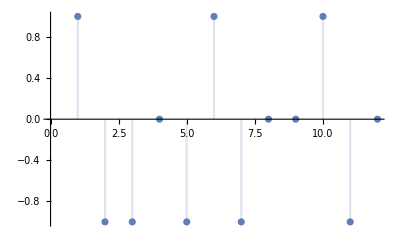

```mathematica
DiscretePlot[MoebiusMu[k],{k,12},AxesOrigin->{0,0}]
```

## *Moebius Function of order k: μ_k

### Definition

The Moebius function of order k is defined as follows:
if n > 1 write n as n = ∏_(i=1)^k (p^α_i)_i and
	μ_k(1) = 1;
	μ_k(n)=0 if p^(k+1)/n
	μ_k(n) = (-1)^r if n=p_1^k p_2^k((⋯p)_r)^k Π p_i^a_i; 0≤a_i<k
	μ(n) = 1 otherwise.

#### Example

```mathematica
TableForm[Table[{n,nMoebiusMu[2,n],nMoebiusMu[3,n]},{n,1,18}],TableHeadings->{None,{"n","μ_2[n]","μ_3[n]"}},TableAlignments->{Right}]
```

n | μ_2[n] | μ_3[n]
1 | 1 | 1
2 | 1 | 1
3 | 1 | 1
4 | -1 | 1
5 | 1 | 1
6 | 1 | 1
7 | 1 | 1
8 | 0 | -1
9 | -1 | 1
10 | 1 | 1
11 | 1 | 1
12 | -1 | 1
13 | 1 | 1
14 | 1 | 1
15 | 1 | 1
16 | 0 | 0
17 | 1 | 1
18 | -1 | 1

## Euler totient Function: ϕ

### Definition

If n ≳ 1 the Euler totient ϕ(n) is defined to be the number of positive integers not exceeding n which are relatively prime to n.

Sum formula: n = ∑_(d/n) ϕ(d)

	n = ∑_(d/n) ϕ(d)
	ϕ(n) = ∑_(d/n) μ(n/d)d

Product formula: write n as n = ∏_(i=1)^k (p^α_i)_i and
	ϕ(n) = n∏_(i=1)^k (1-1/p_i) 
	
Properties
	ϕ(p^a)= p^a-p^(a-1)
	ϕ(m n)=ϕ(m)ϕ(n)d/(ϕ(d))

#### Example

```mathematica
TableForm[Table[{k,EulerPhi[k]},{k,1,20}],TableHeadings->{None,{"k","ϕ[k]"}},TableAlignments->{Right}]
```

k | ϕ[k]
1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
11 | 10
12 | 4
13 | 12
14 | 6
15 | 8
16 | 8
17 | 16
18 | 6
19 | 18
20 | 8

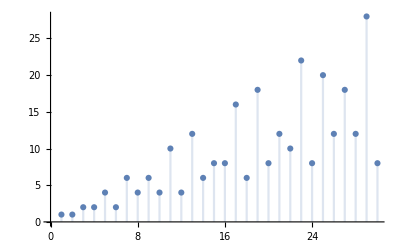

```mathematica
DiscretePlot[EulerPhi[k],{k,30},AxesOrigin->{0,0}]
```

```mathematica
Total[Map[EulerPhi[#]&,Divisors[100]]]
```

100

```mathematica
Divisors[100]
EulerPhi[100]
Total[Map[MoebiusMu[100/#]#&,Divisors[100]]]
```

{1,2,4,5,10,20,25,50,100}

40

40

#### Inverse

```mathematica
Table[DirichletConvolve[EulerPhi[k],DirichletConvolve[1,j MoebiusMu[j],j,k],k,n],{n,1,10}]
```

{1,0,0,0,0,0,0,0,0,0}

## Multiplicative Identity Function: I

### Definition

The Multiplicative Identity Function is defined by I(n) = ⌊1/n⌋.
So I(n) = 1 if n=1 , I(n) = 0 if n≠1.

#### Example

```mathematica
Table[{k,Floor[1/k]},{k,1,4}]//tf
```

1 | 1
2 | 0
3 | 0
4 | 0

## Unit Function: 1

### Definition

The Unit Function is defined by 1(n) = 1.

#### Example

```mathematica
Table[{k,1},{k,1,4}]//tf
```

1 | 1
2 | 1
3 | 1
4 | 1

## Divisor Sum: σ_α

### Definition

For real or complex a and any integer n > 1 we define σ_a as the sum of the a-th powers of the divisors of n.

	σ_a = ∑_(d/n) d^a

#### Example

```mathematica
TableForm[Table[{k,DivisorSigma[1,k]},{k,1,20}],TableHeadings->{None,{"k","σ[k]"}},TableAlignments->{Right}]
```

k | σ[k]
1 | 1
2 | 3
3 | 4
4 | 7
5 | 6
6 | 12
7 | 8
8 | 15
9 | 13
10 | 18
11 | 12
12 | 28
13 | 14
14 | 24
15 | 24
16 | 31
17 | 18
18 | 39
19 | 20
20 | 42

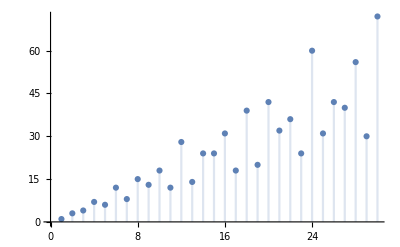

```mathematica
DiscretePlot[DivisorSigma[1,k],{k,30},AxesOrigin->{0,0}]
```

```mathematica
DivisorSigma[0,6]
DivisorSigma[0,35]
DivisorSigma[0,210]
```

4

4

16

#### Inverse

```mathematica
Table[DirichletConvolve[DivisorSigma[2,k],DirichletConvolve[j^2 MoebiusMu[j],MoebiusMu[j],j,k],k,n],{n,1,10}]
```

{1,0,0,0,0,0,0,0,0,0}

## Mangoldt Function: Λ

### Definition

```mathematica
ClearAll[ml]
ml[n_]:=If[PrimePowerQ[n],Log[FactorInteger[n][[1,1]]],0]
```

```mathematica
DirichletConvolve[MangoldtLambda[k],1,k,10]//Simplify
```

Log[10]

#### Example

```mathematica
Table[{k,ml[k],MangoldtLambda[k],DirichletConvolve[MangoldtLambda[k],Floor[1/n],n,k]},{k,1,10}]//tf
```

1 | 0 | 0 | 0
2 | Log[2] | Log[2] | Log[2]
3 | Log[3] | Log[3] | Log[3]
4 | Log[2] | Log[2] | Log[2]
5 | Log[5] | Log[5] | Log[5]
6 | 0 | 0 | 0
7 | Log[7] | Log[7] | Log[7]
8 | Log[2] | Log[2] | Log[2]
9 | Log[3] | Log[3] | Log[3]
10 | 0 | 0 | 0

Log[100]

## Liouville’s Function: λ

### Definition

The Unit Function is defined by λ(n) = (-1)^(Ω(n)).

#### Example

```mathematica
Table[{k,(-1)^PrimeOmega[k]},{k,1,10}]//tf
```

1 | 1
2 | -1
3 | -1
4 | 1
5 | -1
6 | 1
7 | -1
8 | -1
9 | 1
10 | 1

```mathematica
Table[{n,DirichletConvolve[MoebiusMu[k]^2,LiouvilleLambda[k],k,n]},{n,1,11}]//tf
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0
11 | 0

## *Jordan Totient Function: J_k

### Definition

The Jordan Totient function is a generalization of the Euler Totient defined by J(n) = n^k ∏_(i=1)^k (1-p_i^-k).

#### Alternative Defintions:

J_k=N^k*μ = σ_k*μ *μ = σ_k* μ^{2}

```mathematica
Table[{k,nJordanTotient[2,k],nDirichletProduct[{DivisorSigma[2,#]&,MoebiusMu,MoebiusMu}][k],nDirichletProduct[MoebiusMu,#^2&][k]},{k,1,12}]//tf
```

1 | 1 | 1 | 1
2 | 3 | 3 | 3
3 | 8 | 8 | 8
4 | 12 | 12 | 12
5 | 24 | 24 | 24
6 | 24 | 24 | 24
7 | 48 | 48 | 48
8 | 48 | 48 | 48
9 | 72 | 72 | 72
10 | 72 | 72 | 72
11 | 120 | 120 | 120
12 | 96 | 96 | 96

#### Property:

J_k* 1=N^k

```mathematica
Table[{k,k^2,nDirichletProduct[nJordanTotient[2,#]&,1&][k]},{k,1,5}]//tf
```

1 | 1 | 1
2 | 4 | 4
3 | 9 | 9
4 | 16 | 16
5 | 25 | 25

```mathematica
ClearAll[f]
f[n_]:=Sum[nJordanTotient[2,i]Floor[n/i],{i,1,n}]
Table[{k,f[k],nFaulhaber[2,k]},{k,1,5}]//tf
```

1 | 1 | 1
2 | 5 | 5
3 | 14 | 14
4 | 30 | 30
5 | 55 | 55

#### Default Example:

```mathematica
EulerPhi[100]
nJordanTotient[1,100] 
nJordanTotient[100]
```

40

40

40

#### Example:

```mathematica
?nDirichletProduct
```

## *Dedekind Psi Funtion: ψ

## Dirichlet Multiplication ( Convolution )

### Definition

The Dirichlet convolution (f *g)(m) of two functions f(n) and g(n) is given by ∑_(d∣m) f(d) g(m/d).

#### Example

```mathematica
DirichletConvolve[EulerPhi[n],1,n,m]
```

m

```mathematica
DirichletConvolve[n,MoebiusMu[n],n,m]
```

EulerPhi[m]

```mathematica
DirichletConvolve[1,1,n,m]
```

DivisorSigma[0,m]

```mathematica
DirichletConvolve[1,n,n,m]
```

DivisorSigma[1,m]

```mathematica
DirichletConvolve[Log[n],MoebiusMu[n],n,m]
```

MangoldtLambda[m]

```mathematica
f[k_]:=DirichletConvolve[MoebiusMu[n]^2,1,n,k]
Table[{k,2^PrimeNu[k],f[k]},{k,208,212}]//tf
```

208 | 4 | 4
209 | 4 | 4
210 | 16 | 16
211 | 2 | 2
212 | 4 | 4

## Dirichlet Inverse

### Definition

The inverse function is defined by the following recursive definitions:
	f^(-1)(1)=(f(1))^-1
	f^(-1)(n)=-1/f(1)(∑_(d<n) f(n/d)f^(-1)(d))

#### Example:

```mathematica
Table[{k,nDirichletInverse[nDirichletProduct[LiouvilleLambda[#]&,1&]][k],nDirichletProduct[Abs[MoebiusMu[#]]&,MoebiusMu[#]&][k]},{k,1,12}]//tf
```

1 | 1 | 1
2 | 0 | 0
3 | 0 | 0
4 | -1 | -1
5 | 0 | 0
6 | 0 | 0
7 | 0 | 0
8 | 0 | 0
9 | -1 | -1
10 | 0 | 0
11 | 0 | 0
12 | 0 | 0

```mathematica
Table[{k,GCD[12,k],nDirichletInverse[GCD[12,#]&][k],GCD[12,k]MoebiusMu[k]},{k,1,12}]//tf
```

1 | 1 | 1 | 1
2 | 2 | -2 | -2
3 | 3 | -3 | -3
4 | 4 | 0 | 0
5 | 1 | -1 | -1
6 | 6 | 6 | 6
7 | 1 | -1 | -1
8 | 4 | 4 | 0
9 | 3 | 6 | 0
10 | 2 | 2 | 2
11 | 1 | -1 | -1
12 | 12 | 0 | 0

#### Example ( table 3 GT paper Delany )

```mathematica
f[n_]:=Exp[MangoldtLambda[n]]
f1[n_]:=nPrimeProduct[n,#&]
g[n_]:=nDirichletInverse[Function[a,nPrimeProduct[a,#&]]][n]
Table[{k,
f[k],
f1[k],
g[k],
nDirichletProduct[f,g][k]
},{k,1,16}]//tf
```

1 | 1 | 1 | 1 | 1
2 | 2 | 2 | -2 | 0
3 | 3 | 3 | -3 | 0
4 | 2 | 2 | 2 | 0
5 | 5 | 5 | -5 | 0
6 | 1 | 6 | 6 | -5
7 | 7 | 7 | -7 | 0
8 | 2 | 2 | -2 | 0
9 | 3 | 3 | 6 | 0
10 | 1 | 10 | 10 | -9
11 | 11 | 11 | -11 | 0
12 | 1 | 6 | -6 | 5
13 | 13 | 13 | -13 | 0
14 | 1 | 14 | 14 | -13
15 | 1 | 15 | 15 | -14
16 | 2 | 2 | 2 | 0

## *Dirichlet Power

### Definition

The Dirichlet power of an arithmetic function is defined as follows:
	f^(0)(n)=I(n)
	f^(1)(n)=f(n)
	f^(2)(n)=(f*f)(n)		
	f^(-1)(n)=Inverse(f)(n)
	f^(-2)(n)=Inverse(f*f)(n)	
	f^(p/q)(n)=See :Root

#### Example

```mathematica
Table[{k,nDirichletPower[1&,k][4]},{k,1,5}]
```

{{1,1},{2,3},{3,6},{4,10},{5,15}}

```mathematica
Table[{k,nDirichletPower[#&,k][4]},{k,1,5}]
```

{{1,4},{2,12},{3,24},{4,40},{5,60}}

```mathematica
DirichletConvolve[nDirichletPower[MoebiusMu[#]&,2][j],DivisorSigma[0,j],j,1]
```

1

## *Dirichlet Root

### Definition

The Dirichlet root of an arithmetic function is defined as follows:
	f^(p/q)(n)=g(n), s.t f^(p)=g^(q).

#### Example

```mathematica
Table[{k,nDirichletRoot[1&,3][k],nDirichletPower[1&,1/3][k]},{k,1,12}]//tf
```

1 | 1 | 1
2 | 1/3 | 1/3
3 | 1/3 | 1/3
4 | 2/9 | 2/9
5 | 1/3 | 1/3
6 | 1/9 | 1/9
7 | 1/3 | 1/3
8 | 14/81 | 14/81
9 | 2/9 | 2/9
10 | 1/9 | 1/9
11 | 1/3 | 1/3
12 | 2/27 | 2/27

## Multiplicative Functions

### Definition

An arithmetical function is multiplicative if 
	f(a b) = f(a) f(b) if (a,b)=1.

#### Properties

∑_(d|n) μ(d)f(d)=∏_(p|n) (1-f(p))

#### Example

```mathematica
ClearAll[mlAF];
mlAF[n_,fun_]:=Apply[Times,Map[Total[fun[#[[1]]^Array[#-1&,#[[2]]+1]]]&,FactorInteger[n]]]
mlAF[9,MoebiusMu[#]^2/#&]
```

4/3

## *Anti-Multiplicative Functions

### Definition

The multiplicative component of a function f is the function g defined by:
	g(p_1^k_1 p_2^k_2… p_r^k_r)=∏_(i=1)^r f(p_i^k_i).
	
The anti-multiplicative component of a function f is the function h such that
f = g * h. We compute h as h = f * g^(-1).

#### Example-1

```mathematica
ClearAll[f,g,h,gh]
f[n_]:=ⅇ^MangoldtLambda[n]
g[n_]:=nMultiplicativeComponent[f][n]
h[n_]:=nAntiMultiplicativeComponent[f][n]
gh[n_]:=nDirichletProduct[g,h][n]
Table[{k,f[k],g[k],h[k],gh[k]},{k,1,12}]//tf
```

1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 0 | 2
3 | 3 | 3 | 0 | 3
4 | 2 | 2 | 0 | 2
5 | 5 | 5 | 0 | 5
6 | 1 | 6 | -5 | 1
7 | 7 | 7 | 0 | 7
8 | 2 | 2 | 0 | 2
9 | 3 | 3 | 0 | 3
10 | 1 | 10 | -9 | 1
11 | 11 | 11 | 0 | 11
12 | 1 | 6 | 5 | 1

#### Example-2

```mathematica
ClearAll[f,g,h,gh]
f[n_]:=nEulerPhi[2,n]
f[n_]:=nCore[n]
f[n_]:=2^PrimeNu[n]
f[n_]:=GCD[12,n]
f[n_]:=LCM[12,n]
f[n_]:=LiouvilleLambda[n]
f[n_]:=nDirichletProduct[LiouvilleLambda,1&][n]
f[n_]:=nDirichletProduct[#&,#&][n]
f[n_]:=n^2
g[n_]:=nMultiplicativeComponent[f][n]
h[n_]:=nAntiMultiplicativeComponent[f][n]
gh[n_]:=nDirichletProduct[g,h][n]
Table[{k,f[k],g[k],h[k],gh[k],nDirichletProduct[nJordanTotient[2,#]&,1&][k],nDirichletProduct[DivisorSigma[2,#]&,MoebiusMu][k]},{k,1,12}]//tf
```

1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 4 | 0 | 4 | 4 | 4
3 | 9 | 9 | 0 | 9 | 9 | 9
4 | 16 | 16 | 0 | 16 | 16 | 16
5 | 25 | 25 | 0 | 25 | 25 | 25
6 | 36 | 36 | 0 | 36 | 36 | 36
7 | 49 | 49 | 0 | 49 | 49 | 49
8 | 64 | 64 | 0 | 64 | 64 | 64
9 | 81 | 81 | 0 | 81 | 81 | 81
10 | 100 | 100 | 0 | 100 | 100 | 100
11 | 121 | 121 | 0 | 121 | 121 | 121
12 | 144 | 144 | 0 | 144 | 144 | 144

#### Example-3

```mathematica
ClearAll[f,g,h,gh]
f[n_]:=n^2
f[n_]:=1/n
f[n_]:=PrimeNu[n]+Floor[1/n]
g[n_]:=nMultiplicativeComponent[f][n]
h[n_]:=nAntiMultiplicativeComponent[f][n]
gh[n_]:=nDirichletProduct[g,h][n]
Table[{k,f[k],g[k],h[k],gh[k]},{k,1,12}]//tf
2 3 5 7 11
```

1 | 1 | 1 | 1 | 1
2 | 1 | 1 | 0 | 1
3 | 1 | 1 | 0 | 1
4 | 1 | 1 | 0 | 1
5 | 1 | 1 | 0 | 1
6 | 2 | 1 | 1 | 2
7 | 1 | 1 | 0 | 1
8 | 1 | 1 | 0 | 1
9 | 1 | 1 | 0 | 1
10 | 2 | 1 | 1 | 2
11 | 1 | 1 | 0 | 1
12 | 2 | 1 | 0 | 2

2310

## Generalized Convolutions

### Definition

The Generalized Dirichlet convolution (α∘F)(x) of two functions α(n) and F(x) is given by ∑_(n⩽x) α(n) F(x/n).

#### Example-1: Definition

```mathematica
ClearAll[a,f,g,h];
a[n_]:=DivisorSigma[0,n]
h[x_]:=Piecewise[{{0,x<1},{1/x,x≥1}}]
genConvolveMap[fn1_,fn2_,x_]:=Sum[fn1[k]fn2[x/k],{k,1,x}]

genConvolveMap[DivisorSigma[0,#]&,h,4]
genConvolveMap[1&,genConvolveMap[1&,h,#]&,4]

genConvolveMap[DivisorSigma[0,#]&,g,4]
genConvolveMap[1&,genConvolveMap[1&,g,#]&,4]
```

23/4

23/4

3 g[1]+2 g[4/3]+2 g[2]+g[4]

3 g[1]+2 g[4/3]+2 g[2]+g[4]

### Theorem: If G(x)=∑_(n⩽x) α(n) F(x/n) Then F(x)=∑_(n⩽x) α^-1(n) G(x/n)

### Theorem: If α is completely multiplicative Then G=α∘F ⇔ F=(μ ⋆α)∘G

## Bell Series

### Definition

Given an arithmetical function f and a prime p, we denote by f_p(x) the formal power series:
	f_p(x) = ∑_(n=0)^∞ f(p^n)x^n
	
Bell series of the Dirichlet product of two arithmetical functions: if h=f*g then h_p(x)=f_p(x)g_p(x).

#### Example-1

```mathematica
Table[{k,nBellSeriesCoefficient[(1-x)/(1-# x)&,k],nBellSeriesCoefficient[1/(1-# x)&,k]},{k,1,12}]//tf
```

1 | 1 | 1
2 | 1 | 2
3 | 2 | 3
4 | 2 | 4
5 | 4 | 5
6 | 2 | 6
7 | 6 | 7
8 | 4 | 8
9 | 6 | 9
10 | 4 | 10
11 | 10 | 11
12 | 4 | 12

#### Example-2 // BUG 1/ ( (1-x) (1+x) )

```mathematica
Table[{k,nBellSeriesCoefficient[Piecewise[{{(-1-x-2 x^2)/(-1+x),#==2},{(-1-2 x)/(-1+x),#==3},{1,#≠2 ||#≠3}}]&,k],
GCD[12,k],2^PrimeNu[k],nBellSeriesCoefficient[1/((1-x)(1+x))&,k]},{k,1,12}]//tf
```

1 | 1 | 1 | 1 | 0
2 | 2 | 2 | 2 | 0
3 | 3 | 3 | 2 | 0
4 | 4 | 4 | 2 | 1
5 | 1 | 1 | 2 | 0
6 | 6 | 6 | 4 | 0
7 | 1 | 1 | 2 | 0
8 | 4 | 4 | 2 | 0
9 | 3 | 3 | 2 | 1
10 | 2 | 2 | 4 | 0
11 | 1 | 1 | 2 | 0
12 | 12 | 12 | 4 | 0

## *Harmonic Numbers: H

```mathematica
ClearAll[r,s,t,t1,t2,t3,t4]
r[n_]:=Binomial[(n+1)!+n,n]
s[n_]:=(r[n]-1)/((n+1)!)
t[n_]:=s[n]-(n+1)Floor[s[n]/(n+1)]
t1[n_]:=Mod[s[n],n+1]
t2[n_]:=Expand[Pochhammer[x+1,n]][[2]]/(x n!)
t3[n_]:=-StirlingS1[n+1,2]/StirlingS1[n+1,1]
t4[n_]:=Mod[Pochhammer[(n+1)!,n+1]/(n! ((n+1)!)^2)-1/((n+1)!),n+1]
```

```mathematica
1764/720
HarmonicNumber[6]
t[6]
t1[6]
t2[6]
t3[6]
t4[6]
```

49/20

49/20

49/20

«4 more identical outputs»

```mathematica
25 26 27
Pochhammer[25,3]
```

17550

17550

```mathematica
t4[n_]:=Mod[Pochhammer[(n+1)!,n+1]/(n! ((n+1)!)^2)-1/((n+1)!),n+1]
1+1/4+1/9
Expand[(x+1)(x+4)]
Expand[(x+2)(x+3)]
Expand[(x+1)(x+2)(x+3)(x+4)]
(24+50 x+35 x^2+10 x^3+x^4)/(6+5x+x^2)//Simplify
((x+1)(x+2)(x+3)(x+4)(x+1)(x+4))/((x+1)(x+2)(x+3)(x+4))//Simplify//Expand
```

49/36

4+5 x+x^2

6+5 x+x^2

24+50 x+35 x^2+10 x^3+x^4

4+5 x+x^2

4+5 x+x^2

```mathematica
Expand[(x+1)(x/2+1)(x/3+1)(x/4+1)(x/5+1)(x/6+1)]
```

1+(49 x)/20+(203 x^2)/90+(49 x^3)/48+(35 x^4)/144+(7 x^5)/240+x^6/720

```mathematica
HarmonicNumber[4,2]
(7/6)^2
```

205/144

49/36

```mathematica
tt1[n_]:=ⅇ^EulerGamma n Log[Log[n]]
tt1[10^8000]//N
```

1.74923205562703×10^8001

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"bbb0a6ea-c44b-4292-951c-841bc507984b"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","-","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","L*μ","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"a","Number of abelian groups","-","-","?","?","?","?","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | (s-k)/s | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | - | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2/(2 s) | (1+x)/(1-x)
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | L*μ | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
a | Number of abelian groups | - | - | ? | ? | ? | ? | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

## *The Ring and Group of Arithmetical Functions ( needs update )

### Definition: Ring of Arithmetical Functions

Set
	{} Elements: Arithmetical functions
Operations
	+ pointwise addition of functions: (f+g)(n) = f(n)+g(n)
	* Dirichlet multiplication of functions: (f*g) (n)=f(n)*g(n)
Properties
	Commutative ring with identity

### Definition: Group of units U_A

Set
	U_A ={ f ϵ A | f * g = u for some g ϵ  A }.
	It turns out that the units of A are the functions  f ϵ A such that f(1)  =  +/-1.

### Definition: Group of multiplicative functions M_A

Set
	M_A ={ f ϵ A | f(m n) = f(m) f(n) if (m,n)=1 }.
	The multiplicative functions M_A form a subgroup of U_A.

### Definition: Group of functions generated by N, 1.

This group is a subgroup of M_A.

## *Vector Space of Arithmetical Functions

## *Bibliography

## Exercises

### Ram Murty 1.1.9

```mathematica
ClearAll[f,g,h,h1,h2,h3,h4]
g[x_]:=Sum[f[x/n],{n,1,Floor[x]}]
h[x_]:=Sum[g[x/n]MoebiusMu[n],{n,1,Floor[x]}]
h1[x_]:=Sum[Sum[f[(x/n)/k],{k,1,Floor[x/n]}]MoebiusMu[n],{n,1,Floor[x]}]
h2[x_]:=Sum[DivisorSum[n,f[x/n]MoebiusMu[#]&],{n,1,Floor[x]}]
h3[x_]:=Sum[f[x/n]DivisorSum[n,MoebiusMu[#]&],{n,1,Floor[x]}]
h4[x_]:=Sum[f[x/n]Floor[1/n],{n,1,Floor[x]}]
{h[12],h1[12],h2[12],h3[12],h4[12]}
```

{f[12],f[12],f[12],f[12],f[12]}

### Apo 2.1

#### 2.1a

Hint: All odd numbers ...

#### 2.1b

Hint: Powers of 2.

#### 2.1c

{13, 21, 26, 28, 36, 42 }

### Apo 2.2

#### 2.2a

Counter-Example

```mathematica
GCD[35,39]
GCD[EulerPhi[35],EulerPhi[39]]
```

1

24

#### 2.2b

Counter-Example

```mathematica
FactorInteger[35]
GCD[35,EulerPhi[35]]
```

{{5,1},{7,1}}

1

#### 2.2c

Hint

```mathematica
ClearAll[n,m,nm]
n=2^1 3^5 5^2;
m=2^1 3^2 5^1;
nm=2^2 3^7 5^3;
m EulerPhi[n]
n EulerPhi[m]
1/2 2/3 4/5  n m
1/2 2/3 4/5 n m
```

291600

291600

291600

«1 more identical outputs»

### Apo 2.3

```mathematica
HoldForm[n/EulerPhi[n]]//TraditionalForm
HoldForm[(∏_(i=1)^k Subscript[p, i]^Subscript[α, i])/(∏_(i=1)^k Subscript[p, i]^(Subscript[α, i]-1)(Subscript[p, i]-1))]//TraditionalForm
HoldForm[(∏_(i=1)^k Subscript[p, i])/(∏_(i=1)^k Subscript[p, i]-1)]//TraditionalForm
HoldForm[∏_(i=1)^k Subscript[p, i]/(Subscript[p, i]-1)]//TraditionalForm
HoldForm[∏_(i=1)^k 1+1/(Subscript[p, i]-1)]//TraditionalForm
HoldForm[∏_(i=1)^k MoebiusMu[1]^2/EulerPhi[1]+MoebiusMu[Subscript[p, i]]^2/EulerPhi[Subscript[p, i]]+(MoebiusMu[Subscript[p, i]^2]^2)/EulerPhi[Subscript[p, i]^2]+ Etc]//TraditionalForm
HoldForm[∏_(i=1)^k ∑_(j=0)^Subscript[α, i] ((MoebiusMu[Subscript[p, i]^j]^2)/EulerPhi[Subscript[p, i]^j])]//TraditionalForm
HoldForm[∑_(d|n) (MoebiusMu[d]^2/EulerPhi[d])]//TraditionalForm
```

n/n

(∏_(i=1)^k p_i^α_i)/(∏_(i=1)^k p_i^(α_i-1) (p_i-1))

(∏_(i=1)^k p_i)/(∏_(i=1)^k p_i-1)

∏_(i=1)^k p_i/(p_i-1)

∏_(i=1)^k 1+1/(p_i-1)

∏_(i=1)^k 1^2/1+p_i^2/p_i+((p_i^2)^2)/p_i^2+Etc

∏_(i=1)^k ∑_(j=0)^α_i ((p_i^j)^2)/p_i^j

∑_(d|n) d^2/d

### Apo 2.4

```mathematica
2/1 3/2 5/4 7/6 11/10 13/12 17/16 19/18//N
```

5.84713

```mathematica
2/1 3/2 5/4 7/6 11/10 13/12 17/16 19/18 23/22//N
```

6.11291

### Apo 2.5: Revise!

Show that (ω*μ)(n)=Piecewise[{{1, IF n ϵ ℙ}, {0, otherwise}}]

#### Example

```mathematica
Table[{k,DirichletConvolve[PrimeNu[n],MoebiusMu[n],n,k]},{k,1,8}]//tf
```

1 | 0
2 | 1
3 | 1
4 | 0
5 | 1
6 | 0
7 | 1
8 | 0

#### Proof

```mathematica
HoldForm[DirichletConvolve[MoebiusMu[k],PrimeNu[k],k,n]]//TraditionalForm
HoldForm[∑_(d|n) MoebiusMu[d]PrimeNu[n/d]]//TraditionalForm
HoldForm[∑_(d |p^a m) (MoebiusMu[d]PrimeNu[(p^a m)/d])]//TraditionalForm
HoldForm[∑_(k=0)^a (∑_(d p^k|p^a m) (MoebiusMu[d p^k]PrimeNu[(p^a m)/d]))]//TraditionalForm
HoldForm[∑_(d|m) (MoebiusMu[d]PrimeNu[(p^a m)/d])+∑_(d|m) (MoebiusMu[d p]PrimeNu[(p^(a-1)m)/d])+∑_(k=2)^a (∑_(d|m) (MoebiusMu[d p^k]PrimeNu[(p^(a-k)m)/d]))]//TraditionalForm
HoldForm[∑_(d|m) (MoebiusMu[d]PrimeNu[(p^a m)/d])+∑_(d|m) (MoebiusMu[d p]PrimeNu[(p^(a-1)m)/d])]//TraditionalForm
HoldForm[∑_(d|m) (MoebiusMu[d]PrimeNu[(p^a m)/d])+∑_(d|m) (MoebiusMu[p]MoebiusMu[d]PrimeNu[(p^(a-1)m)/d])]//TraditionalForm
HoldForm[∑_(d|m) (MoebiusMu[d]PrimeNu[(p^a m)/d])-∑_(d|m) (MoebiusMu[d]PrimeNu[(p^(a-1)m)/d])]//TraditionalForm
HoldForm[∑_(d|m) (MoebiusMu[d](1+PrimeNu[m/d]))-∑_(d|m) (MoebiusMu[d](1+PrimeNu[m/d]))]//TraditionalForm
```

DirichletConvolve[k,k,k,n]

∑_(d|n) d n/d

∑_(d|p^a m) d (p^a m)/d

∑_(k=0)^a (∑_(d p^k|p^a m) d p^k (p^a m)/d)

∑_(d|m) d (p^a m)/d+∑_(d|m) d p (p^(a-1) m)/d+∑_(k=2)^a (∑_(d|m) d p^k (p^(a-k) m)/d)

∑_(d|m) d (p^a m)/d+∑_(d|m) d p (p^(a-1) m)/d

∑_(d|m) d (p^a m)/d+∑_(d|m) p d (p^(a-1) m)/d

∑_(d|m) d (p^a m)/d-∑_(d|m) d (p^(a-1) m)/d

∑_(d|m) d (1+m/d)-∑_(d|m) d (1+m/d)

#### Test-1 ( Expected Value: 0 )

```mathematica
DirichletConvolve[MoebiusMu[k],PrimeNu[k],k,100]
Total[Map[MoebiusMu[#]PrimeNu[100/#]&,{1,5,25}]]+Total[Map[MoebiusMu[2#]PrimeNu[50/#]&,{1,5,25}]]+Total[Map[MoebiusMu[4#]PrimeNu[25/#]&,{1,5,25}]]
Total[Map[MoebiusMu[#](1+PrimeNu[25/#])&,{1,5,25}]]-Total[Map[MoebiusMu[#](1+PrimeNu[25/#])&,{1,5,25}]]
```

#### Test-2 ( Expected Value: 1)

```mathematica
DirichletConvolve[MoebiusMu[k],PrimeNu[k],k,17]
Total[Map[MoebiusMu[#]PrimeNu[17/#]&,{1}]]+Total[Map[MoebiusMu[17#]PrimeNu[1/#]&,{1}]]
Total[Map[MoebiusMu[#]PrimeNu[17/#]&,{1}]]
```

1

1

1

### Apo 2.6

Hint: ( Zie ook uitleg over d^2/n )

```mathematica
ClearAll[d2n]
d2n[n_,k_]:=Divisors[Apply[Times,Map[(#[[1]])^Floor[(#[[2]])/k]&,FactorInteger[n]]]]
d2n[n_]:=d2n[n,2]
DirichletConvolve[MoebiusMu[n],1,n,Last[d2n[2 3 5 7]]]
DirichletConvolve[MoebiusMu[n],1,n,Last[d2n[10^9+1,3]]]
```

0

0

### Apo 2.7

```mathematica
HoldForm[∑_(d|n) MoebiusMu[d]MoebiusMu[GCD[Subscript[p, 1],d]]]//TraditionalForm
HoldForm[∏_(i=1)^PrimeNu[n] ∑_(j=0)^Subscript[α, i] (MoebiusMu[Subscript[p, i]^j]MoebiusMu[GCD[Subscript[p, 1],Subscript[p, i]^j]])]//TraditionalForm
HoldForm[∑_(j=0)^Subscript[α, 0] (MoebiusMu[Subscript[p, 1]^j]MoebiusMu[GCD[Subscript[p, 1],Subscript[p, 1]^j]])∏_(i=2)^PrimeNu[n] ∑_(j=0)^Subscript[α, i] (MoebiusMu[Subscript[p, i]^j]MoebiusMu[GCD[Subscript[p, 1],Subscript[p, i]^j]])]//TraditionalForm
HoldForm[(MoebiusMu[1]MoebiusMu[GCD[Subscript[p, 1],1]]+MoebiusMu[Subscript[p, 1]]MoebiusMu[GCD[Subscript[p, 1],Subscript[p, 1]]])∏_(i=2)^PrimeNu[n] ∑_(j=0)^Subscript[α, i] (MoebiusMu[Subscript[p, i]^j]MoebiusMu[GCD[Subscript[p, 1],Subscript[p, i]^j]])]//TraditionalForm
HoldForm[(MoebiusMu[1]MoebiusMu[GCD[Subscript[p, 1],1]]+MoebiusMu[Subscript[p, 1]]MoebiusMu[GCD[Subscript[p, 1],Subscript[p, 1]]])∏_(i=2)^PrimeNu[n] ∑_(j=0)^Subscript[α, i] (MoebiusMu[1]MoebiusMu[GCD[Subscript[p, 1],1]]+MoebiusMu[Subscript[p, i]]MoebiusMu[GCD[Subscript[p, 1],Subscript[p, i]]])]//TraditionalForm
HoldForm[(1+1)∏_(i=2)^PrimeNu[n] (1+(-1))]//TraditionalForm
```

∑_(d|n) d gcd(p_1,d)

∏_(i=1)^n ∑_(j=0)^α_i p_i^j gcd(p_1,p_i^j)

∑_(j=0)^α_0 (p_1^j gcd(p_1,p_1^j)) ∏_(i=2)^n ∑_(j=0)^α_i p_i^j gcd(p_1,p_i^j)

(1 gcd(p_1,1)+p_1 gcd(p_1,p_1)) ∏_(i=2)^n ∑_(j=0)^α_i p_i^j gcd(p_1,p_i^j)

(1 gcd(p_1,1)+p_1 gcd(p_1,p_1)) ∏_(i=2)^n ∑_(j=0)^α_i (1 gcd(p_1,1)+p_i gcd(p_1,p_i))

(1+1) ∏_(i=2)^n (1-1)

### Apo 2.8

### Apo 2.9

### Apo 2.10

### Apo 2.11

### Apo 2.12

#### Solution

```mathematica
HoldForm[(∑_(d|n) DivisorSigma[0,d])^2=(∏_(i=1)^PrimeNu[n] ∑_(j=0)^Subscript[α, i] (DivisorSigma[0,Subscript[p, i]^j]))^2]//TraditionalForm
HoldForm[(∑_(d|n) DivisorSigma[0,d])^2=(∏_(i=1)^PrimeNu[n] ((Subscript[α, i]+1)(Subscript[α, i]+2))/2)^2]//TraditionalForm
HoldForm[(∑_(d|n) DivisorSigma[0,d])^2=∏_(i=1)^PrimeNu[n] (((Subscript[α, i]+1)(Subscript[α, i]+2))/2)^2]//TraditionalForm
HoldForm[(∑_(d|n) DivisorSigma[0,d])^2=∏_(i=1)^PrimeNu[n] ∑_(j=0)^Subscript[α, i] (j+1)^3]//TraditionalForm
HoldForm[(∑_(d|n) DivisorSigma[0,d])^2=∏_(i=1)^PrimeNu[n] ∑_(j=0)^Subscript[α, i] DivisorSigma[0,Subscript[p, i]^j]^3]//TraditionalForm
HoldForm[(∑_(d|n) DivisorSigma[0,d])^2=∑_(d|n) DivisorSigma[0,d]^3]//TraditionalForm
```

(∑_(d|n) 0d)^2=(∏_(i=1)^n ∑_(j=0)^α_i 0p_i^j)^2

(∑_(d|n) 0d)^2=(∏_(i=1)^n 1/2 (α_i+1) (α_i+2))^2

(∑_(d|n) 0d)^2=∏_(i=1)^n (1/2 (α_i+1) (α_i+2))^2

(∑_(d|n) 0d)^2=∏_(i=1)^n ∑_(j=0)^α_i (j+1)^3

(∑_(d|n) 0d)^2=∏_(i=1)^n ∑_(j=0)^α_i (0p_i^j)^3

(∑_(d|n) 0d)^2=∑_(d|n) (0d)^3

#### Example

```mathematica
ClearAll[f1,f2,g1,g2,g3]
f1[n_]:=DivisorSum[n,DivisorSigma[0,#]&]
f2[n_]:=DivisorSum[n,DivisorSigma[0,#]^3&]
g1[n_]:=Apply[Times,Map[Function[k,DivisorSum[k,DivisorSigma[0,#]^3&]],Map[(#[[1]])^(#[[2]])&,FactorInteger[n]]]]
g2[n_]:=Apply[Times,Map[Total[Map[#^3&,Range[#[[2]]+1]]]&,FactorInteger[n]]]
g3[n_]:=Apply[Times,Map[((#[[2]]+1)(#[[2]]+2))/2&,FactorInteger[n]]]
f1[210]
f2[210]
g3[210]
(g3[210])^2
```

81

6561

81

6561

```mathematica
DivisorSigma[0,1]+DivisorSigma[0,2]+DivisorSigma[0,4]+DivisorSigma[0,8]
```

10

### Apo 2.13

Hint:

```mathematica
divisorProduct[10,DivisorSigma[0,#]^(10/#)&]
Exp[DivisorSum[10,10/# Log[DivisorSigma[0,#]]&]]
```

512

512

### Apo 2.14a

#### Solution

```mathematica
HoldForm[∑_(d|n) (F[d]MoebiusMu[n/d])]//TraditionalForm
HoldForm[∑_(d|n) (∑_(k=1)^d f[k/d])MoebiusMu[n/d]]//TraditionalForm
HoldForm[∑_(k=1)^n ∑_(d|n) f[k/n]MoebiusMu[d]]//TraditionalForm
HoldForm[∑_("k=1,(n,k)=1")^n f[k/n]]//TraditionalForm
```

∑_(d|n) F(d) n/d

∑_(d|n) (∑_(k=1)^d f(k/d)) n/d

∑_(k=1)^n ∑_(d|n) f(k/n) d

∑_(k=1,(n,k)=1)^n f(k/n)

#### Example

```mathematica
ClearAll[f,g]
f[n_]:=DirichletConvolve[Sum[g[j/k],{j,1,k}],MoebiusMu[k],k,n]
f[12];
f[30]
f[n_]:=DivisorSum[n,Sum[g[j/#],{j,1,#}]MoebiusMu[n/#]&]
f[12];
f[30]
f[n_]:=Sum[DivisorSum[GCD[n,k],g[k/n]MoebiusMu[#]&],{k,1,n}]
f[12];
f[30]
```

g[1/30]+g[7/30]+g[11/30]+g[13/30]+g[17/30]+g[19/30]+g[23/30]+g[29/30]

g[1/30]+g[7/30]+g[11/30]+g[13/30]+g[17/30]+g[19/30]+g[23/30]+g[29/30]

g[1/30]+g[7/30]+g[11/30]+g[13/30]+g[17/30]+g[19/30]+g[23/30]+g[29/30]

### Apo 2.14b

#### Solution

Note  that the function under consideration is equal to I(n). Then simply apply 2.14a

```mathematica
ClearAll[f]
f[n_]:=Sum[Exp[2π ⅈ k/n],{k,1,n}]
Table[{k,f[k]//nc},{k,1,6}]//tf
```

1 | 1.
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0

### Apo 2.15a

### Apo 2.16a

```mathematica
ClearAll[f,g]
f[n_]:=1/2 n DirichletConvolve[j,MoebiusMu[j],j,n]

g[n_]:=nEulerPhi[1,101]
g[n_]:=DirichletConvolve[nFaulhaber[1,j],MoebiusMu[j]j,j,n]
g[n_]:=DirichletConvolve[j(j+1)/2,MoebiusMu[j]j,j,n]
g[n_]:=DirichletConvolve[n(j+1)/2,MoebiusMu[j],j,n]
g[n_]:=1/2 n DirichletConvolve[(j+1),MoebiusMu[j],j,n]
g[n_]:=1/2 n DirichletConvolve[j,MoebiusMu[j],j,n]
g[n_]:=1/2 n EulerPhi[n]
f[101]
g[101]
```

5050

5050

### Apo 2.16b

```mathematica
ClearAll[f,g]
f[n_]:=1/3 n^2 EulerPhi[n]+n/6 primeProduct[n,(1-#)&]
f[n_]:=1/3 n^2 EulerPhi[n]+n/6 DivisorSum[n,MoebiusMu[#]#&]
f[n_]:=DivisorSum[n,MoebiusMu[#] n^3/(3#)&]+DivisorSum[n,MoebiusMu[#] n/6#&]
f[n_]:=DivisorSum[n,MoebiusMu[#](n^3/(3#)+(n #)/6)&]
f[n_]:=DivisorSum[n,MoebiusMu[#]((2 n^3+n #^2)/(6 #))&]

(* What are exactly the functions here, how should the n,j be interpreted *)

f[n_]:=DirichletConvolve[1,MoebiusMu[j]((2 n^3+n j^2)/(6 j)),j,n]
f[n_]:=DirichletConvolve[MoebiusMu[n/j],((2 n^3+n j^2)/(6 j)),j,n]
f[n_]:=DirichletConvolve[MoebiusMu[j],((2 n^3)/(6 n/j)+(n n/j)/6),j,n]
f[n_]:=DirichletConvolve[MoebiusMu[j],((2 n^2 j)/6+(n n)/(6 j)),j,n]
f[n_]:=DirichletConvolve[2 j^3+j,MoebiusMu[j]j^2/6,j,n]+DirichletConvolve[3 j^2,MoebiusMu[j]j^2/6,j,n]
f[n_]:=DirichletConvolve[2 j^3+3 j^2+j,MoebiusMu[j]j^2/6,j,n]
f[n_]:=DirichletConvolve[(j(j+1)(2j+1))/6,MoebiusMu[j] j^2,j,n]
f[n_]:=DirichletConvolve[nFaulhaber[2,j],MoebiusMu[j] j^2,j,n]
f[n_]:=nEulerPhi[2,n]


(* Bezig met d -> j ombouw *)
f[n_]:=DirichletConvolve[1,MoebiusMu[d]((2 n^3+n d^2)/(6 d)),d,n]
f[n_]:=DirichletConvolve[MoebiusMu[n/d],((2 n^3+n d^2)/(6 d)),d,n]
f[n_]:=DirichletConvolve[((2 n^2 d)/6+(n n)/(6 d)),MoebiusMu[d],d,n]
f[n_]:=DirichletConvolve[(2 d^3+d)/6,MoebiusMu[d] d^2,d,n]
f[n_]:=DirichletConvolve[(2 d^3+d)/6,MoebiusMu[d] d^2,d,n]+DirichletConvolve[3 d^2/6,MoebiusMu[d] d^2,d,n]
g[n_]:=nEulerPhi[2,n]

f[15]
g[15]
```

620

620

## Exercises McCarthy

### McC 1.1

### McC 1.2

### McC 1.3

```mathematica
ClearAll[f,g,h1,h2]
g[n_]:=Sum[f[GCD[n,r]],{r,1,n}]
h1[n_]:=DivisorSum[n,g[#]&]
h2[n_]:=DivisorSum[n,# f[n/#]&]
h1[9]
h2[9]
h1[25]
h2[25]
```

9 f[1]+3 f[3]+f[9]

9 f[1]+3 f[3]+f[9]

25 f[1]+5 f[5]+f[25]

25 f[1]+5 f[5]+f[25]

### McC 1.4

```mathematica
ClearAll[f,g]
f[fn1_,fn2_,k_,n_]:=Apply[Plus,Map[fn1[#[[1]]]fn2[#[[2]]]&,Map[#[[1]]&,Select[Map[{#,LCM[#[[1]],#[[2]]]}&,Tuples[Range[n],k]],#[[2]]==n&]]]]
g[n_]:=DirichletConvolve[DirichletConvolve[EulerPhi[j],1,j,k]DirichletConvolve[EulerPhi[j],1,j,k],MoebiusMu[k],k,n]
g[fn1_,fn2_,k_,n_]:=nDirichletProduct[(nDirichletProduct[fn1,1&][#]nDirichletProduct[fn2,1&][#])&,MoebiusMu][n]

nJordanTotient[2,3]
f[EulerPhi,EulerPhi,2,3]
g[EulerPhi,EulerPhi,2,3]
```

8

8

```mathematica
8
```

```mathematica
ClearAll[s,t]
f[s[#]&,t[#]&,2,4]
g[s[#]&,t[#]&,2,4]//Expand
g[1&,1&,2,144]
```

```mathematica
DirichletConvolve[DirichletConvolve[1,1,j,k]DirichletConvolve[1,1,j,k],1,k,6]
nDirichletProduct[(nDirichletProduct[1&,1&][#]nDirichletProduct[1&,1&][#])&,1&][6]
```

25

```mathematica
25
```

```mathematica
h[fn1_,fn2_,k_,n_]:=Select[Map[{#,LCM[#[[1]],#[[2]]]}&,Tuples[Range[n],k]],#[[2]]==n&]
Map[#[[1]]&,h[EulerPhi,EulerPhi,2,6]]
Map[#[[1]]&,h[EulerPhi,EulerPhi,2,2]]Map[#[[1]]&,h[EulerPhi,EulerPhi,2,3]]
```

{{1,6},{2,3},{2,6},{3,2},{3,6},{6,1},{6,2},{6,3},{6,6}}

{{1,6},{6,1},{6,6}}

```mathematica
ClearAll[s,t]
f[s[#]&,t[#]&,2,2]
g[s[#]&,t[#]&,2,2]
g[s[#]&,t[#]&,2,2]//Expand
```

s[2] t[1]+s[1] t[2]+s[2] t[2]

-s[1] t[1]+(s[1]+s[2]) (t[1]+t[2])

s[2] t[1]+s[1] t[2]+s[2] t[2]

3. Averages of Arithmetical Functions

## EulerGamma Constant

#### Example-1

```mathematica
ClearAll[f]
f[x_]:=Sum[1/k,{k,1,x}]-Integrate[1/y,{y,1,x}]
Limit[f[x],x->Infinity]
```

EulerGamma

```mathematica
f[10000]//N
g[10000]//N
```

0.577266

0.577166

```mathematica
N[EulerGamma,16]
```

0.5772156649015329

```mathematica
f[1]
f[10]//N
```

1

0.626383

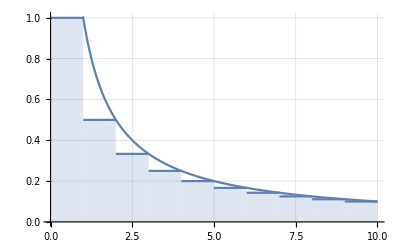

```mathematica
Clear[pl]
pl[x_]:=Show[DiscretePlot[f[k],{k,1,Floor[x]}],DiscretePlot[1/k,{k,1,Floor[x]},ExtentSize->Left],Plot[1/y,{y,.4,x}],GridLines->Automatic,PlotRange->Full,AxesOrigin->{0,0}]
pl[10]
```

#### Example-2: Alternatief in ontwikkeling

```mathematica
ClearAll[f,g]
D[Log[n+1],{n,1}]
Integrate[1/(y+1),{y,0,1}]//N
f[x_]:=Sum[1/k,{k,1,x}]-Integrate[1/(y+1),{y,0,x}]
g[n_]:=HarmonicNumber[n]-Log[n+1]
Limit[f[x],x->Infinity]
Limit[g[x],x->Infinity]
```

1/(1+n)

0.693147

EulerGamma

EulerGamma

## Some Elementary Asymptotic Formulas

### Theorem: ⌊x/n ⌋= x/n+O(1)

### Theorem: ∑_(n≤ x) 1/n = Log(x)+γ +O(1/x)

#### Proof

```mathematica
HoldForm[Integrate[f[t],{t,1,x}]+Integrate[(t-Floor[t])f'[t],{t,1,x}]+f[1]+(Floor[x]-x)f[x]]//TraditionalForm
HoldForm[Integrate[1/t,{t,1,x}]+Integrate[(t-Floor[t])-1/t^2,{t,1,x}]+1+(Floor[x]-x)/x]//TraditionalForm
HoldForm[Log[x]+1-Integrate[(t-Floor[t])1/t^2,{t,1,x}]-(x-Floor[x])/x]//TraditionalForm
HoldForm[Log[x]+1-Integrate[(t-Floor[t])1/t^2,{t,1,x}]+O[1/x]]//TraditionalForm
HoldForm[Log[x]+1-Integrate[(t-Floor[t])1/t^2,{t,1,Infinity}]+Integrate[(t-Floor[t])1/t^2,{t,x,Infinity}]+O[1/x]]//TraditionalForm
HoldForm[Log[x]+(1-Integrate[(t-Floor[t])1/t^2,{t,1,Infinity}])+O[1/x]]//TraditionalForm
HoldForm[Log[x]+EulerGamma+O[1/x]]//TraditionalForm
```

∫_1^x f(t)ⅆt+∫_1^x (t-Floor[t]) f'(t)ⅆt+f(1)+(Floor[x]-x) f(x)

∫_1^x 1/t ⅆt+∫_1^x ((t-Floor[t])-1/t^2)ⅆt+1+(Floor[x]-x)/x

log(x)+1-∫_1^x (t-Floor[t])/t^2 ⅆt-(x-Floor[x])/x

log(x)+1-∫_1^x (t-Floor[t])/t^2 ⅆt+O(1/x)

log(x)+1-∫_1^∞ (t-Floor[t])/t^2 ⅆt+∫_x^∞ (t-Floor[t])/t^2 ⅆt+O(1/x)

log(x)+(1-∫_1^∞ (t-Floor[t])/t^2 ⅆt)+O(1/x)

log(x)+ℽ+O(1/x)

#### Example

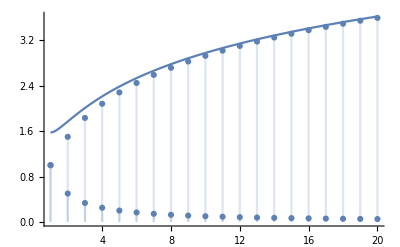

```mathematica
ClearAll[pl]
pl[n_]:=Show[DiscretePlot[1/x,{x,1,n}],DiscretePlot[Sum[1/y,{y,1,x}],{x,1,n}],Plot[Log[x]+EulerGamma+ 1/x,{x ,1,n}],PlotRange->All]
pl[20]
```

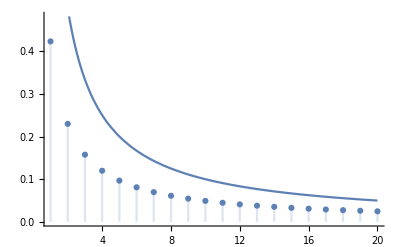

True

```mathematica
pl1[n_]:=Show[DiscretePlot[{Sum[1/y,{y,1,x}]-(Log[x]+EulerGamma )},{x,1,n}],Plot[ 1/x,{x ,1,n}],PlotRange->All,AxesOrigin->{0,0}]
pl1[20]
(Sum[1/y,{y,1,20}]-(Log[20]+EulerGamma))<1/20
```

### Theorem: ∑_(n≤ x) ⌊x/n ⌋ = x Log(x)+O(x)

#### Proof

```mathematica
HoldForm[Sum[Floor[x/k],{k,1,x}]]//TraditionalForm
HoldForm[Sum[x/k+O[1],{k,1,x}]]//TraditionalForm
HoldForm[x Sum[1/k,{k,1,x}]+Sum[O[1],{k,1,x}]]//TraditionalForm
HoldForm[x(Log[x]+EulerGamma+O[1/x])+x O[1]]//TraditionalForm
HoldForm[x Log[x]+EulerGamma x+ O[x]]//TraditionalForm
HoldForm[x Log[x]+ O[x]]//TraditionalForm
```

∑_(k=1)^x Floor[x/k]

∑_(k=1)^x (x/k+O(1))

x ∑_(k=1)^x 1/k+∑_(k=1)^x O(1)

x (log(x)+ℽ+O(1/x))+x O(1)

x log(x)+ℽ x+O(x)

x log(x)+O(x)

#### Example

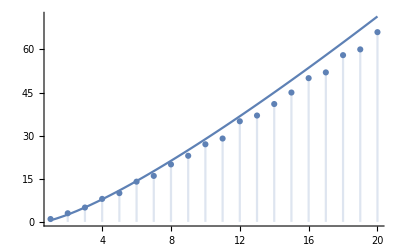

```mathematica
ClearAll[f,pl];
f[n_]:=Sum[Floor[n/j],{j,1,n}]
pl[n_]:=Show[DiscretePlot[Sum[Floor[k/j],{j,1,k}],{k,1,n}],Plot[ x Log[x]+ x EulerGamma ,{x,1,n}],AxesOrigin->{0,0},PlotRange->All]
pl[20]
```

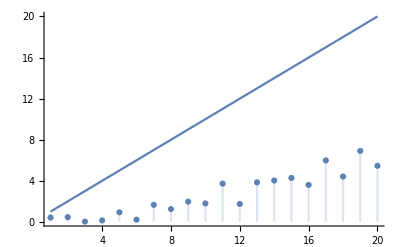

```mathematica
pl1[n_]:=Show[DiscretePlot[Abs[{Sum[Floor[x/j],{j,1,x}]-(x Log[x]+x EulerGamma )}],{x,1,n}],Plot[ x,{x ,1,n}],PlotRange->All,AxesOrigin->{0,0}]
pl1[20]
```

### Theorem: ∑_(n≤ x) 1/n^s = x^(1-s)/(1-s)+ζ(s) +O(1/x^s)

#### Proof

```mathematica
HoldForm[Integrate[f[t],{t,1,x}]+Integrate[(t-Floor[t])f'[t],{t,1,x}]+f[1]+(Floor[x]-x)f[x]]//TraditionalForm
HoldForm[Integrate[1/t^s,{t,1,x}]-s Integrate[(t-Floor[t])/t^(s+1),{t,1,x}]+1-(x-Floor[x])/x]//TraditionalForm
HoldForm[Integrate[1/t^s,{t,1,x}]+1-s Integrate[(t-Floor[t])/t^(s+1),{t,1,x}]+O[1/x^s]]//TraditionalForm
HoldForm[x^(1-s)/(1-s)-1/(1-s)+1-s Integrate[(t-Floor[t])/t^(s+1),{t,1,x}]+O[1/x^s]]//TraditionalForm
HoldForm[x^(1-s)/(1-s)+(1-1/(1-s)-s Integrate[(t-Floor[t])/t^(s+1),{t,1,x}])+O[1/x^s]]//TraditionalForm
HoldForm[x^(1-s)/(1-s)+Zeta[s]+O[1/x^s]]//TraditionalForm
```

∫_1^x f(t)ⅆt+∫_1^x (t-Floor[t]) f'(t)ⅆt+f(1)+(Floor[x]-x) f(x)

∫_1^x 1/t^s ⅆt-s ∫_1^x (t-Floor[t])/t^(s+1)ⅆt+1-(x-Floor[x])/x

∫_1^x 1/t^s ⅆt+1-s ∫_1^x (t-Floor[t])/t^(s+1)ⅆt+O(1/x^s)

x^(1-s)/(1-s)-1/(1-s)+1-s ∫_1^x (t-Floor[t])/t^(s+1)ⅆt+O(1/x^s)

x^(1-s)/(1-s)+(1-1/(1-s)-s ∫_1^x (t-Floor[t])/t^(s+1)ⅆt)+O(1/x^s)

x^(1-s)/(1-s)+s+O(1/x^s)

#### Example

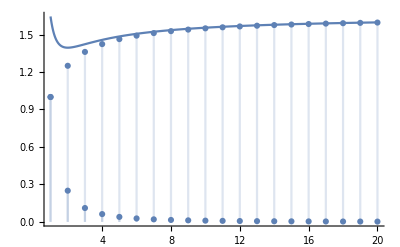

```mathematica
ClearAll[pl]
pl[n_,s_]:=Show[DiscretePlot[1/x^s,{x,1,n}],DiscretePlot[Sum[1/y^s,{y,1,x}],{x,1,n}],Plot[x^(1-s)/(1-s)+Zeta[s]+ 1/x^s,{x ,1,n}],PlotRange->All]
pl[20,2]
```

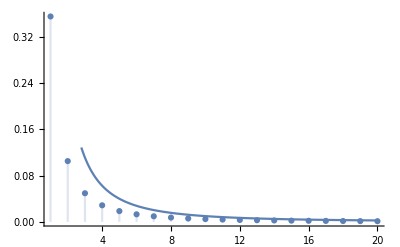

True

```mathematica
pl1[n_,s_]:=Show[DiscretePlot[{Sum[1/y^s,{y,1,x}]-(x^(1-s)/(1-s)+Zeta[s])},{x,1,n}],Plot[ 1/x^s,{x ,1,n}],PlotRange->All,AxesOrigin->{0,0}]
pl1[20,2]
(Sum[1/y^2,{y,1,20}]-(20^-1/-1+Zeta[2]))<1/10^2
```

### Theorem: ∑_(n>x) 1/n^s = O(x^(1-s))

#### Proof

```mathematica
HoldForm[Zeta[s]-(x^(1-s)/(1-s)+Zeta[s]+O[1/x^s])]//TraditionalForm
HoldForm[x^(1-s)/(s-1)+O[1/x^s]]//TraditionalForm
HoldForm[O[x^(1-s)]]//TraditionalForm
```

s-(x^(1-s)/(1-s)+s+O(1/x^s))

x^(1-s)/(s-1)+O(1/x^s)

O(x^(1-s))

### Theorem: ∑_(n≤ x) n^α =x^(α+1)/(α+1)+O(x^α )

#### Proof

```mathematica
HoldForm[Integrate[f[t],{t,1,x}]+Integrate[(t-Floor[t])f'[t],{t,1,x}]+f[1]+(Floor[x]-x)f[x]]//TraditionalForm
HoldForm[Integrate[t^α,{t,1,x}]+Integrate[(t-Floor[t])α t^(α-1),{t,1,x}]+1+(Floor[x]-x)x^α]//TraditionalForm
HoldForm[x^(α+1)/(α+1)-1/(α+1)+Integrate[(t-Floor[t])α t^(α-1),{t,1,x}]+1+(Floor[x]-x)x^α]//TraditionalForm
HoldForm[x^(α+1)/(α+1)-1/(α+1)+O[α Integrate[ t^(α-1),{t,1,x}]]+1+O[x^α]]//TraditionalForm
HoldForm[x^(α+1)/(α+1)-1/(α+1)+O[-1+x^α]+1+O[x^α]]//TraditionalForm
HoldForm[x^(α+1)/(α+1)+O[x^α]]//TraditionalForm
```

∫_1^x f(t)ⅆt+∫_1^x (t-Floor[t]) f'(t)ⅆt+f(1)+(Floor[x]-x) f(x)

∫_1^x t^α ⅆt+∫_1^x (t-Floor[t]) α t^(α-1)ⅆt+1+(Floor[x]-x) x^α

x^(α+1)/(α+1)-1/(α+1)+∫_1^x (t-Floor[t]) α t^(α-1)ⅆt+1+(Floor[x]-x) x^α

x^(α+1)/(α+1)-1/(α+1)+O(α ∫_1^x t^(α-1)ⅆt)+1+O(x^α)

x^(α+1)/(α+1)-1/(α+1)+O(-1+x^α)+1+O(x^α)

x^(α+1)/(α+1)+O(x^α)

#### Example

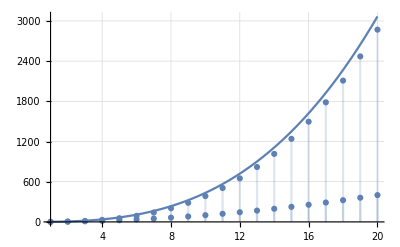

```mathematica
ClearAll[pl]
pl[n_,a_]:=Show[DiscretePlot[x^a,{x,1,n}],DiscretePlot[Sum[y^a,{y,1,x}],{x,1,n}],Plot[x^(a+1)/(a+1)+x^a,{x ,1,n}],PlotRange->All,GridLines->Automatic]
pl[20,2]
```

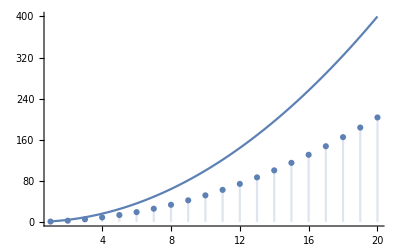

True

```mathematica
pl1[n_,a_]:=Show[DiscretePlot[{Sum[y^a,{y,1,x}]-x^(a+1)/(a+1)},{x,1,n}],Plot[ x^a ,{x ,1,n}],PlotRange->All,AxesOrigin->{0,0}]
pl1[20,2]
(Sum[1/y,{y,1,20}]-20^3/3)<20^2
```

## Asymptotic Formulas for Arithmetical Functions

### Theorem: ∑_(n≤ x) τ(n) = x Log(x)+(2γ-1)x +O(√x)

#### Introduction

Formulas for calculating ∑_(n≤ x) τ(n)

```mathematica
ClearAll[nDiv1,nDiv2,nDiv3,nDiv4];
nDiv1[z_]:=Sum[DivisorSigma[0,y],{y,1,Floor[z]}]
nDiv2[z_]:=Total[Map[Length[Solve[y==#/x&&x>0&&y>0,{x,y},Integers]]&,Range[Floor[z]]]]
nDiv3[z_]:=Total[Map[Floor[z/#]&,Range[Floor[z]]]]
nDiv4[z_]:=2Sum[Floor[z/k]-k,{k,1,Floor[Sqrt[z]]}]+Floor[√z]
{nDiv1[10],nDiv2[10],nDiv3[10],nDiv4[10]}
```

{27,27,27,27}

#### Proof

```mathematica
HoldForm[2Sum[Floor[x/k]-k,{k,1,Floor[Sqrt[x]]}]+Floor[√x]]//TraditionalForm
HoldForm[2Sum[x/k-k+O[1],{k,1,Floor[Sqrt[x]]}]+O[√x]]//TraditionalForm
HoldForm[2Sum[x/k,{k,1,Floor[Sqrt[x]]}]-2Sum[k,{k,1,Floor[Sqrt[x]]}]+O[√x]]//TraditionalForm
HoldForm[2x Sum[1/k,{k,1,Floor[Sqrt[x]]}]-2Sum[k,{k,1,Floor[Sqrt[x]]}]+O[√x]]//TraditionalForm
HoldForm[2x  (Log[√x]+γ +O[1/(√x)])-2Sum[k,{k,1,Floor[Sqrt[x]]}]+O[√x]]//TraditionalForm
HoldForm[x  Log[x]+2γ  x -2Sum[k,{k,1,Floor[Sqrt[x]]}]+O[√x]]//TraditionalForm
HoldForm[x  Log[x]+2γ  x -2(x/2+O[√x])+O[√x]]//TraditionalForm
HoldForm[x  Log[x]+(2γ -1) x +O[√x]]//TraditionalForm
```

2 ∑_(k=1)^Floor[√x] (Floor[x/k]-k)+Floor[√x]

2 ∑_(k=1)^Floor[√x] (x/k-k+O(1))+O(√x)

2 ∑_(k=1)^Floor[√x] x/k-2 ∑_(k=1)^Floor[√x] k+O(√x)

2 x ∑_(k=1)^Floor[√x] 1/k-2 ∑_(k=1)^Floor[√x] k+O(√x)

2 x (log(√x)+γ+O(1/(√x)))-2 ∑_(k=1)^Floor[√x] k+O(√x)

x log(x)+2 γ x-2 ∑_(k=1)^Floor[√x] k+O(√x)

x log(x)+2 γ x-2 (x/2+O(√x))+O(√x)

x log(x)+(2 γ-1) x+O(√x)

#### Example

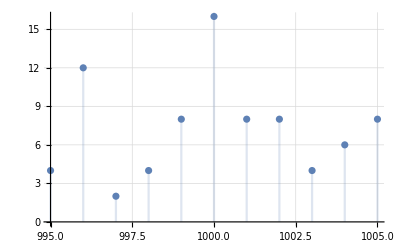

```mathematica
ClearAll[pl0]
pl0[n_,m_]:=Show[DiscretePlot[DivisorSigma[0,x],{x,n,m}],GridLines->Automatic,PlotRange->All]
pl0[995,1005]
```

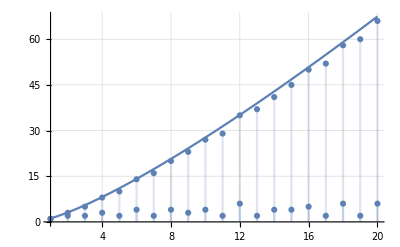

```mathematica
ClearAll[pl]
pl[n_]:=Show[
DiscretePlot[DivisorSigma[0,x],{x,1,n}],
DiscretePlot[Sum[DivisorSigma[0,y],{y,1,x}],{x,1,n}],
Plot[x Log[x]+x(2 EulerGamma -1 )+ √x,{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[20]
```

True

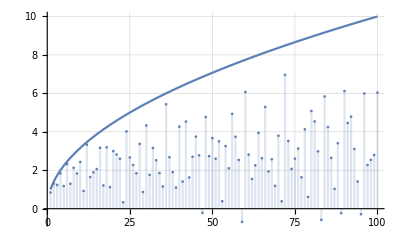

```mathematica
pl1[n_]:=Show[DiscretePlot[{Sum[DivisorSigma[0,y],{y,1,x}]-(x Log[x]+(2 EulerGamma -1 )x)},{x,1,n}],Plot[ √x,{x ,1,n}],PlotRange->All,GridLines->Automatic,AxesOrigin->{0,0}]
Sum[DivisorSigma[0,y],{y,1,100}]-(100Log[100]+(2EulerGamma-1)100)<√100
pl1[100]
```

### Theorem: ∑_(n≤ x) σ(n) = 1/2 ζ(2)x^2+O(x Log(x))

#### Introduction

Formulas for calculating ∑_(n≤ x) σ(n)

```mathematica
ClearAll[nDiv1,nDiv2,nDiv3,nDiv4];
nDiv1[z_]:=Sum[DivisorSigma[1,y],{y,1,Floor[z]}]
nDiv2[z_]:=Total[Map[#[[1,2]]&,Flatten[Map[Map[#&,Solve[y==#/x&&x>0&&y>0,{x,y},Integers]]&,Range[Floor[z]]],1]]]
nDiv3[z_]:=Total[Map[# Floor[z/#]&,Range[Floor[z]]]]
nDiv4[z_]:=Sum[Sum[q,{q,1,Floor[z/d]}],{d,1,Floor[z]}]
{nDiv1[6],nDiv2[6],nDiv3[6],nDiv4[6]}
```

{33,33,33,33}

#### Proof

```mathematica
HoldForm[Sum[Sum[q,{q,1,Floor[x/d]}],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[1/2(x/d)^2+O[x/d],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[1/2 x^2 Sum[1/d^2,{d,1,Floor[x]}]+O[x Sum[1/d,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[1/2 x^2(-1/x+Zeta[2]+O[1/x^2])+O[x Sum[1/d,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[1/2 x^2(-1/x+Zeta[2]+O[1/x^2])+O[x Log[x]]]//TraditionalForm
HoldForm[1/2 Zeta[2] x^2+O[x Log[x]]]//TraditionalForm
```

∑_(d=1)^Floor[x] (∑_(q=1)^Floor[x/d] q)

∑_(d=1)^Floor[x] (1/2 (x/d)^2+O(x/d))

1/2 x^2 ∑_(d=1)^Floor[x] 1/d^2+O(x ∑_(d=1)^Floor[x] 1/d)

1/2 x^2 (-1/x+2+O(1/x^2))+O(x ∑_(d=1)^Floor[x] 1/d)

1/2 x^2 (-1/x+2+O(1/x^2))+O(x log(x))

(2 x^2)/2+O(x log(x))

#### Example

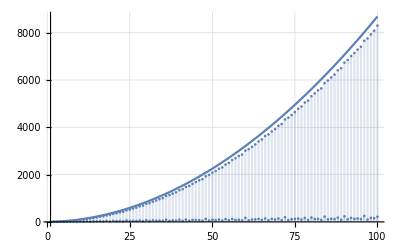

```mathematica
ClearAll[pl]
pl[n_]:=Show[DiscretePlot[DivisorSigma[1,x],{x,1,n}],DiscretePlot[Sum[DivisorSigma[1,y],{y,1,x}],{x,1,n}],Plot[1/2 Zeta[2] x^2+x Log[x],{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[100]
```

True

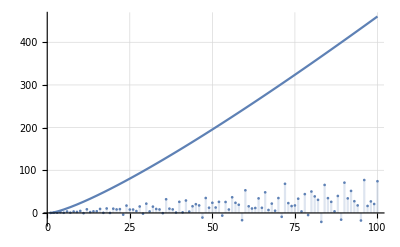

```mathematica
pl1[n_]:=Show[DiscretePlot[{Sum[DivisorSigma[1,y],{y,1,x}]-1/2 Zeta[2] x^2},{x,1,n}],Plot[ x Log[x],{x ,1,n}],PlotRange->All,GridLines->Automatic,AxesOrigin->{0,0}]
Sum[DivisorSigma[1,y],{y,1,100}]-(1/2 100^2 Zeta[2])<100Log[100]
pl1[100]
```

### Theorem: ∑_(n≤ x) σ_α(n) = 1/(α+1)ζ(α+1)x^2+O(x^Max[1,α])

#### Introduction

Formulas for calculating ∑_(n≤ x) σ_α(n)

```mathematica
ClearAll[nDiv1,nDiv4];
nDiv1[z_,a_]:=Sum[DivisorSigma[a,y],{y,1,Floor[z]}]
nDiv4[z_,a_]:=Sum[Sum[q^a,{q,1,Floor[z/d]}],{d,1,Floor[z]}]
{nDiv1[6,2],nDiv4[6,2]}
```

{113,113}

#### Proof

```mathematica
HoldForm[Sum[Sum[q^α,{q,1,Floor[x/d]}],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[1/(α+1)(x/d)^(α+1)+O[x^α/d^α],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[1/(α+1) x^(α+1) Sum[1/d^(α+1),{d,1,Floor[x]}]+O[x^α Sum[1/d^α,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[1/(α+1) x^(α+1)(x^-α/-α+Zeta[α+1]+O[x^(-α-1)])+O[x^α (x^(1-α)/(1-α)+Zeta[α]+O[x^-α])]]//TraditionalForm
HoldForm[1/(α+1) Zeta[α+1] x^(α+1)+O[x]+O[1]+O[x^α]]//TraditionalForm
HoldForm[1/(α+1) Zeta[α+1] x^(α+1)+O[x^Max[1,α]]]//TraditionalForm
```

∑_(d=1)^Floor[x] (∑_(q=1)^Floor[x/d] q^α)

∑_(d=1)^Floor[x] ((x/d)^(α+1)/(α+1)+O(x^α/d^α))

(x^(α+1) ∑_(d=1)^Floor[x] 1/d^(α+1))/(α+1)+O(x^α ∑_(d=1)^Floor[x] 1/d^α)

(x^(α+1) (-x^-α/α+α+1+O(x^(-α-1))))/(α+1)+O(x^α (x^(1-α)/(1-α)+α+O(x^-α)))

(α+1 x^(α+1))/(α+1)+O(x)+O(1)+O(x^α)

(α+1 x^(α+1))/(α+1)+O(x^(max(1,α)))

#### Example

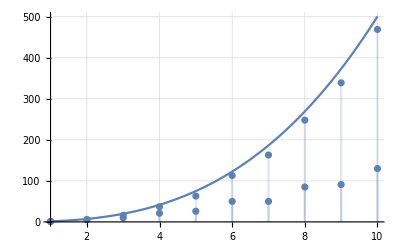

```mathematica
ClearAll[pl]
pl[n_,a_]:=Show[DiscretePlot[DivisorSigma[a,x],{x,1,n}],DiscretePlot[Sum[DivisorSigma[a,y],{y,1,x}],{x,1,n}],Plot[1/(a+1)Zeta[a+1] x^(a+1)+x^Max[1,a],{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[10,2]
```

### Theorem: ∑_(n≤ x) σ_-β(n) = ζ(β+1)x+O(x^Max[0,1-β]) if β≠1

#### Introduction

Formulas for calculating ∑_(n≤ x) σ_-β(n)

```mathematica
ClearAll[nDiv1,nDiv4];
nDiv1[z_,b_]:=Sum[DivisorSigma[-b,y],{y,1,Floor[z]}] 
nDiv4[z_,b_]:=Sum[Sum[q^-b,{q,1,Floor[z/d]}],{d,1,Floor[z]}]
nDiv4A[z_,b_]:=Sum[1/d^b Sum[1,{q,1,Floor[z/d]}],{d,1,Floor[z]}]
{nDiv1[6,2],nDiv4[6,2],nDiv4A[6,2]}
```

{2841/400,2841/400,2841/400}

#### Proof

```mathematica
HoldForm[Sum[1/d^b Sum[1,{q,1,Floor[x/d]}],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[1/d^b(x/d+O[1]),{d,1,Floor[x]}]]//TraditionalForm
HoldForm[x Sum[1/d^(b+1),{d,1,Floor[x]}]+O[Sum[1/d^b,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[x^(1-b)/-b Zeta[b+1]x+O[x^-b]]//TraditionalForm
HoldForm[ Zeta[b+1]x+O[x^Max[0,1-b]]]//TraditionalForm
```

∑_(d=1)^Floor[x] (∑_(q=1)^Floor[x/d] 1)/d^b

∑_(d=1)^Floor[x] (x/d+O(1))/d^b

x ∑_(d=1)^Floor[x] 1/d^(b+1)+O(∑_(d=1)^Floor[x] 1/d^b)

-(x^(1-b) b+1 x)/b+O(x^-b)

b+1 x+O(x^(max(0,1-b)))

#### Example

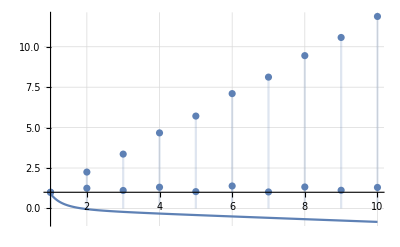

```mathematica
ClearAll[pl]
pl[n_,b_]:=Show[
DiscretePlot[DivisorSigma[b,x],{x,1,n}],
DiscretePlot[Sum[DivisorSigma[b,y],{y,1,x}],{x,1,n}],
Plot[Zeta[b+1]x+1/x^(1-b),{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[10,-2]
```

### Theorem: ∑_(n≤ x) ϕ(n) = 3/π^2 x^2+O(x Log[x])

#### Introduction

Formulas for calculating ∑_(n≤ x) ϕ(n)

```mathematica
ClearAll[nPhi1,nPhi2];
nPhi1[z_]:=Sum[EulerPhi[y],{y,1,Floor[z]}]
nPhi2[z_]:=Sum[MoebiusMu[d]Sum[q,{q,1,Floor[z/d]}],{d,1,Floor[z]}]
{nPhi1[50],nPhi2[50]}
```

{774,774}

#### Proof

```mathematica
HoldForm[Sum[MoebiusMu[d]Sum[q,{q,1,Floor[x/d]}],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[ Sum[MoebiusMu[d](1/2(x/d)^2+O[x/d]),{d,1,Floor[x]}]]//TraditionalForm
HoldForm[1/2 x^2 Sum[MoebiusMu[d]/d^2,{d,1,Floor[x]}]+O[x Sum[1/d,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[1/2 x^2 6/π^2+O[x Sum[1/d,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[3/π^2 x^2+O[x Log[x]]]//TraditionalForm
```

∑_(d=1)^Floor[x] d ∑_(q=1)^Floor[x/d] q

∑_(d=1)^Floor[x] d (1/2 (x/d)^2+O(x/d))

1/2 x^2 ∑_(d=1)^Floor[x] d/d^2+O(x ∑_(d=1)^Floor[x] 1/d)

(x^2 6)/(2 π^2)+O(x ∑_(d=1)^Floor[x] 1/d)

(3 x^2)/π^2+O(x log(x))

#### Example

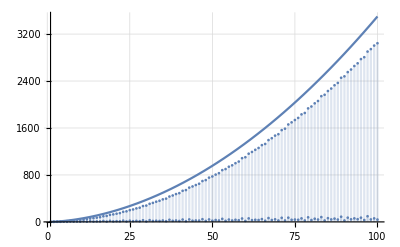

```mathematica
ClearAll[pl]
pl[n_]:=Show[DiscretePlot[EulerPhi[x],{x,1,n}],DiscretePlot[Sum[EulerPhi[y],{y,1,x}],{x,1,n}],Plot[3/π^2 x^2+x Log[x],{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[100]
```

True

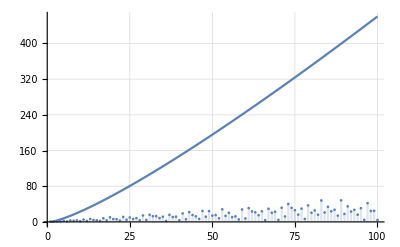

```mathematica
pl1[n_]:=Show[DiscretePlot[{
Sum[EulerPhi[y],{y,1,x}]-3/π^2 x^2},{x,1,n}],Plot[ x Log[x],{x ,1,n}],PlotRange->All,GridLines->Automatic,AxesOrigin->{0,0}]
Sum[EulerPhi[y],{y,1,100}]-(3/π^2 100^2)<100Log[100]
pl1[100]
```

## An application to the distribution of lattice points visible from the origin

### Theorem: Two lattice points (a,b) and (m,n) are mutually visible if,and only if,a—m and b—n are relatively prime.

### Theorem: The set of lattice points visible from the origin has density 6/π^2.

#### Introduction

We will show that r→^limit∞ (N'(r))/(N(r))= 6/π^2
where 
	N(r) = # Lattice points in square with height/width r,
	N’(r)= # Visible lattice points in that square.
The quotient N/N’ represents the density of visible lattice points.
The square is defined by 
	{ (x,y) :|x|⩽r,|y|⩽r  }.
Note that the 8 lattice points nearest the origin are all visible from the origin. 
By symmetry, we see that  N’(r) is equal to 8, plus 8 times the number of visible points in the region 
	{ (x,y) : 2 ⩽ x ⩽ r, 1 ⩽ y ⩽ x}.

#### Proof

```mathematica
HoldForm[Limit[N'[r]/N[r],r->Infinity]]//TraditionalForm
HoldForm[Limit[(8(Sum[EulerPhi[n],{n,1,Floor[r]}]))/(2 Floor[r]+1)^2,r->Infinity]]//TraditionalForm
HoldForm[Limit[(8(3/π^2 r^2+O[r Log[r]]))/(2 Floor[r]+1)^2,r->Infinity]]//TraditionalForm
HoldForm[Limit[(8(3/π^2 r^2+O[r Log[r]]))/(4 r^2+O[r]),r->Infinity]]//TraditionalForm
HoldForm[Limit[(24/π^2 r^2+O[r Log[r]])/(4 r^2+O[r]),r->Infinity]]//TraditionalForm
HoldForm[Limit[(6/π^2+O[Log[r]/r])/(1+O[1/r]),r->Infinity]]//TraditionalForm
HoldForm[6/π^2]//TraditionalForm
```

(N'(r))/N[r]r∞

(8 ∑_(n=1)^Floor[r] n)/(2 Floor[r]+1)^2r∞

(8 ((3 r^2)/π^2+O(r log(r))))/(2 Floor[r]+1)^2r∞

(8 ((3 r^2)/π^2+O(r log(r))))/(4 r^2+O(r))r∞

((24 r^2)/π^2+O(r log(r)))/(4 r^2+O(r))r∞

(6/π^2+O((log(r))/r))/(1+O(1/r))r∞

6/π^2

## Partial Sums of a Dirichlet Product

### Theorem: If F(x) = ∑_(n⩽x) f(n) Then ∑_(n⩽x) ∑_(d/n) f(d)=∑_(n⩽x) f(n)⌊x/n⌋=∑_(n⩽x) F(x/n)

#### Proof

```mathematica
ClearAll[sf1, formatsf1];
formatsf1[ls_List]:=Module[{max,tmp,out},
max=Max[Map[Length[#]&,ls]];
out=Map[Fold[Append,#,Array[0&,max-Length[#]]]&,ls];
tmp=Reap[Map[Append[#,Sow[Total[#]]]&,out]];
out=Map[Append[#,Total[#]]&,out];
out=Append[out,Append[Array[0&,max],Total[tmp[[2,1]]]]];
out=ReplaceRepeated[out,0->""];
TableForm[out,TableHeadings->{Append[Range[Length[ls]],"T"],Append[Map[StringJoin["d",ToString[#]]&,Range[max]],"T"]}]
]
sf1[n_,fun_]:=Map[fun[#]&,Map[Divisors[#]&,Range[n]],{2}] (* old version *)
sf1[n_,fun_]:=Table[Map[ReleaseHold[fun[#]]&,Divisors[k]],{k,1,n}]
```

```mathematica
ClearAll[sf2, formatsf2];
formatsf2[ls_List]:=Module[{out},
out=ls;
out=Append[out,{Total[ls[[All,1]]]}];
TableForm[out,TableHeadings->{Append[Range[Length[ls]],"T"],{1}}]
]
sf2[n_,fun_]:=Map[{fun[#] Floor[n/#]}&,Range[n]]
```

```mathematica
ClearAll[sf3, formatsf3];
formatsf3[ls_List]:=Module[{max,tmp,out},
max=Max[Map[Length[#]&,ls]];
out=Map[Fold[Append,#,Array[0&,max-Length[#]]]&,ls];
out=Map[Append[#,Total[#]]&,out];
out=Transpose[out];
out=Map[Append[#,Total[#]]&,out];
out=Transpose[out];
out=Append[ReplaceRepeated[out[[1;;max]],0->""],out[[max+1]]];
TableForm[out,TableHeadings->{Append[Range[Length[ls]],"T"],Append[Map[#&,Range[max]],"T"]}]
]
sf3[n_,fun_]:=Map[Map[fun[#]&,Range[Floor[n/#]]]&,Range[n]]
```

```mathematica
ClearAll[sf4, sfAll,sd];
ClearAll[sd];
sd[n_,fun_]:=Total[Map[fun[#]&,Divisors[n]]]
sf4[n_,fn1_,fn2_]:=(fn1[#1] (fn2[#1]&)/@Range[Floor[n/#1]]&)/@Range[n]
sfAll[n_,fun_]:={sf1[n,fun[#]&]//formatsf1,sf2[n,fun[#]&]//formatsf2,sf3[n,fun[#]&]//formatsf3}//tf
```

#### Example

```mathematica
Table[{DirichletConvolve[MoebiusMu[n],n,n,k]},{k,1,10}]//formatsf2
```

| 1
1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
T | 32

```mathematica
Table[{EulerPhi[k]},{k,1,10}]//formatsf2
```

| 1
1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
T | 32

```mathematica
Table[{sd[k,Function[j,(k/j) MoebiusMu[j]]]},{k,1,10}]//formatsf2
```

| 1
1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
T | 32

```mathematica
sf1[10,HoldForm[MoebiusMu[#]Floor[k/#]]&]//formatsf1 
sf1[10,HoldForm[DirichletConvolve[MoebiusMu[#]Floor[k/#],Floor[1/n],n,#]]&]//formatsf1
```

| d1 | d2 | d3 | d4 | T
1 | 1 |  |  |  | 1
2 | 2 | -1 |  |  | 1
3 | 3 | -1 |  |  | 2
4 | 4 | -2 |  |  | 2
5 | 5 | -1 |  |  | 4
6 | 6 | -3 | -2 | 1 | 2
7 | 7 | -1 |  |  | 6
8 | 8 | -4 |  |  | 4
9 | 9 | -3 |  |  | 6
10 | 10 | -5 | -2 | 1 | 4
T |  |  |  |  | 32

| d1 | d2 | d3 | d4 | T
1 | 1 |  |  |  | 1
2 | 2 | -1 |  |  | 1
3 | 3 | -1 |  |  | 2
4 | 4 | -2 |  |  | 2
5 | 5 | -1 |  |  | 4
6 | 6 | -3 | -2 | 1 | 2
7 | 7 | -1 |  |  | 6
8 | 8 | -4 |  |  | 4
9 | 9 | -3 |  |  | 6
10 | 10 | -5 | -2 | 1 | 4
T |  |  |  |  | 32

```mathematica
sf2[10,Boole[MemberQ[Divisors[10],#]]&]//formatsf2
```

| 1
1 | 10
2 | 5
3 | 0
4 | 0
5 | 2
6 | 0
7 | 0
8 | 0
9 | 0
10 | 1
T | 18

```mathematica
sf3[6,DirichletConvolve[MoebiusMu[k],k,k,#]&]//formatsf3
```

| 1 | 2 | 3 | 4 | 5 | 6 | T
1 | 1 | 1 | 2 | 2 | 4 | 2 | 12
2 | 1 | 1 | 2 |  |  |  | 4
3 | 1 | 1 |  |  |  |  | 2
4 | 1 |  |  |  |  |  | 1
5 | 1 |  |  |  |  |  | 1
6 | 1 |  |  |  |  |  | 1
T | 6 | 3 | 4 | 2 | 4 | 2 | 21

### Theorem: ∑_(k⩽n) ∑_(d/k) f(d) (k/d)^m= ∑_(k⩽n) ∑_(d/k) f(k/d) d^m =∑_(k⩽n) f(k)Faulhaber[m,⌊x/n⌋] where Faulhaber[m,n]=(BernoulliB[m+1,n+1]-BernoulliB[m+1,1])/(m+1)

#### Proof

#### Example

```mathematica
Table[{sd[k,Function[j, j(k/j)^3]]},{k,1,6}]//formatsf2
Table[{sd[k,Function[j, (k/j)j^3]]},{k,1,6}]//formatsf2
Table[{k,k faulhaber[3,Floor[6/k]]},{k,1,6}]//tf
```

| 1
1 | 1
2 | 10
3 | 30
4 | 84
5 | 130
6 | 300
T | 555

| 1
1 | 1
2 | 10
3 | 30
4 | 84
5 | 130
6 | 300
T | 555

1 | 441
2 | 72
3 | 27
4 | 4
5 | 5
6 | 6

### Theorem: ∑_(n⩽x) μ(n) ⌊x/n⌋=1

### Theorem: ∑_(n⩽x) Λ(n) ⌊x/n⌋=Log(⌊x⌋!)

### Theorem: | ∑_(n⩽x) (μ(n))/n |⩽1

### Theorem: Legendre's Identity : ⌊x⌋! = ∏_(p⩽x) p^(α(p))

#### Proof

```mathematica
ClearAll[f]
f[n_,p_]:=Sum[Floor[n/p^i],{i,1,Ceiling[N[Log[n]]/Log[p]]}]/;p≤n
g[n_]:=Times@@Map[#^f[n,#]&,Select[Range[n],PrimeQ]]
```

```mathematica
5!
g[5]
```

120

120

### Theorem: ∑_(n⩽x) Λ(n) ⌊x/n⌋=Log(⌊x⌋!)= ∑_(n⩽x) Log n =x Log x - x + O(Log x)

### Theorem: ∑_(p⩽x) Log[p] ⌊x/p⌋=x Log x + O(x)

### Theorem: If (a>0, b>0, ab=x) Then ∑_(q d⩽x) f(d)g(q)=∑_(n⩽a) f(n)G(⌊x/n⌋) +∑_(n⩽b) g(n)F(⌊x/n⌋) - F(a)G(b)

### Theorem: ∑_(n⩽x) ϕ(n)=1/2 x^2/(ζ(2)) + O(x Log(x))

### Theorem: ∑_(n⩽x) (ϕ(n))/n=x/(ζ(2)) + O(Log(x))

## Exercises

### Apo 3.1 a)

```mathematica
HoldForm[Sum[Log[n]/n,{n,1,Floor[x]}]]//TraditionalForm
HoldForm[Integrate[f[t],{t,1,x}]+Integrate[(t-Floor[t])f'[t],{t,1,x}]+f[1]+(Floor[x]-x)f[x]]//TraditionalForm
HoldForm[Integrate[Log[t]/t,{t,1,x}]+Integrate[(t-Floor[t])(1-Log[t])/t^2,{t,1,x}]+Log[1]/1+(Floor[x]-x)Log[x]/x]//TraditionalForm
HoldForm[Log[x]^2/2+Integrate[(t-Floor[t])(1-Log[t])/t^2,{t,1,x}]+O[Log[x]/x]]//TraditionalForm
HoldForm[Log[x]^2/2+Integrate[(t-Floor[t])(1-Log[t])/t^2,{t,1,Infinity}]-Integrate[(t-Floor[t])(1-Log[t])/t^2,{t,x,Infinity}]+O[Log[x]/x]]//TraditionalForm
HoldForm[Log[x]^2/2+A-O[Integrate[(1-Log[t])/t^2,{t,x,Infinity}]]+O[Log[x]/x]]//TraditionalForm
HoldForm[Log[x]^2/2+A+O[Log[x]/x]+O[Log[x]/x]]//TraditionalForm
HoldForm[Log[x]^2/2+A+O[Log[x]/x]]//TraditionalForm
```

∑_(n=1)^Floor[x] (log(n))/n

∫_1^x f(t)ⅆt+∫_1^x (t-Floor[t]) f'(t)ⅆt+f(1)+(Floor[x]-x) f(x)

∫_1^x (log(t))/t ⅆt+∫_1^x ((t-Floor[t]) (1-log(t)))/t^2 ⅆt+log(1) 1/1+((Floor[x]-x) log(x))/x

(log^2(x))/2+∫_1^x ((t-Floor[t]) (1-log(t)))/t^2 ⅆt+O((log(x))/x)

(log^2(x))/2+∫_1^∞ ((t-Floor[t]) (1-log(t)))/t^2 ⅆt-∫_x^∞ ((t-Floor[t]) (1-log(t)))/t^2 ⅆt+O((log(x))/x)

(log^2(x))/2+A-O(∫_x^∞ (1-log(t))/t^2 ⅆt)+O((log(x))/x)

(log^2(x))/2+A+O((log(x))/x)+O((log(x))/x)

(log^2(x))/2+A+O((log(x))/x)

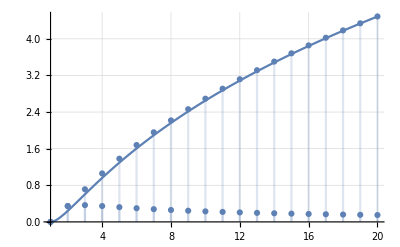

```mathematica
ClearAll[pl]
pl[n_]:=Show[
DiscretePlot[Log[x]/x,{x,1,n}],
DiscretePlot[Sum[Log[y]/y,{y,1,x}],{x,1,n}],
Plot[Log[x]^2/2,{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[20]
```

### Apo 3.1 b)

```mathematica
D[1/(t Log[t]),{t,1}]//Simplify
Integrate[1/(t Log[t]),{t,2,x}]
-Log[Log[2]]//N
Integrate[(1+Log[t])/(t^2 Log[t]^2),{t,2,x}]
```

-(1+Log[t])/(t^2 Log[t]^2)

ConditionalExpression[-Log[Log[2]]+Log[Log[x]], Re[x]>1||x∉ℝ]

0.366513

ConditionalExpression[1/Log[4]-1/(x Log[x]), Re[x]>1||x∉ℝ]

```mathematica
HoldForm[Sum[1/(n Log[n]),{n,1,Floor[x]}]]//TraditionalForm
HoldForm[Integrate[f[t],{t,1,x}]+Integrate[(t-Floor[t])f'[t],{t,2,x}]+f[2]+(Floor[x]-x)f[x]]//TraditionalForm
HoldForm[Integrate[1/(t Log[t]),{t,2,x}]+Integrate[(t-Floor[t])-(1+Log[t])/(t^2 Log[t]^2),{t,2,x}]+1/(2Log[2])+(Floor[x]-x)1/(x Log[x])]//TraditionalForm
HoldForm[Log[Log[x]]-Log[Log[2]]+Integrate[(Floor[t]-t)(1+Log[t])/(t^2 Log[t]^2),{t,2,x}]+1/(2Log[2])+O[1/(x Log[x])]]//TraditionalForm
HoldForm[Log[Log[x]]-Log[Log[2]]+Integrate[(Floor[t]-t)(1+Log[t])/(t^2 Log[t]^2),{t,2,Infinity}]-Integrate[(Floor[t]-t)(1+Log[t])/(t^2 Log[t]^2),{t,x,Infinity}]+1/(2Log[2])+O[1/(x Log[x])]]//TraditionalForm
HoldForm[Log[Log[x]]-(Log[Log[2]]+1/(2Log[2])+Integrate[(Floor[t]-t)(1+Log[t])/(t^2 Log[t]^2),{t,2,Infinity}])-O[Integrate[(1+Log[t])/(t^2 Log[t]^2),{t,x,Infinity}]]+O[1/(x Log[x])]]//TraditionalForm
HoldForm[Log[Log[x]]+B-O[Integrate[(1+Log[t])/(t^2 Log[t]^2),{t,x,Infinity}]]+O[1/(x Log[x])]]//TraditionalForm
HoldForm[Log[Log[x]]+B+O[1/(x Log[x])]+O[1/(x Log[x])]]//TraditionalForm
HoldForm[Log[Log[x]]+B+O[1/(x Log[x])]]//TraditionalForm
```

∑_(n=1)^Floor[x] 1/(n log(n))

∫_1^x f(t)ⅆt+∫_2^x (t-Floor[t]) f'(t)ⅆt+f(2)+(Floor[x]-x) f(x)

∫_2^x 1/(t log(t))ⅆt+∫_2^x ((t-Floor[t])-(1+log(t))/(t^2 log^2(t)))ⅆt+1/(2 log(2))+(Floor[x]-x)/(x log(x))

log(log(x))-log(log(2))+∫_2^x ((Floor[t]-t) (1+log(t)))/(t^2 log^2(t))ⅆt+1/(2 log(2))+O(1/(x log(x)))

log(log(x))-log(log(2))+∫_2^∞ ((Floor[t]-t) (1+log(t)))/(t^2 log^2(t))ⅆt-∫_x^∞ ((Floor[t]-t) (1+log(t)))/(t^2 log^2(t))ⅆt+1/(2 log(2))+O(1/(x log(x)))

log(log(x))-(log(log(2))+1/(2 log(2))+∫_2^∞ ((Floor[t]-t) (1+log(t)))/(t^2 log^2(t))ⅆt)-O(∫_x^∞ (1+log(t))/(t^2 log^2(t))ⅆt)+O(1/(x log(x)))

log(log(x))+B-O(∫_x^∞ (1+log(t))/(t^2 log^2(t))ⅆt)+O(1/(x log(x)))

log(log(x))+B+O(1/(x log(x)))+O(1/(x log(x)))

log(log(x))+B+O(1/(x log(x)))

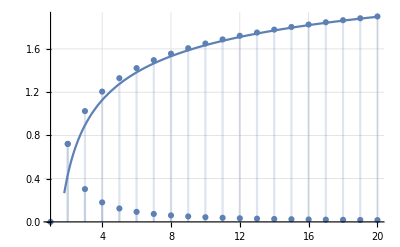

```mathematica
ClearAll[pl]
pl[n_]:=Show[
DiscretePlot[1/(x Log[x]),{x,1,n}],
DiscretePlot[Sum[1/(y Log[y]),{y,2,x}],{x,1,n}],
Plot[Log[Log[x]]+0.8,{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[20]
```

### Apo 3.2)

```mathematica
ClearAll[f]
f[x_]:=Sum[1/d Sum[1/q,{q,1,Floor[x/d]}],{d,1,Floor[x]}]
f[6]
```

269/60

```mathematica
HoldForm[Sum[DivisorSigma[0,n]/n,{n,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[1/d Sum[1/q,{q,1,Floor[x/d]}],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[1/d(Log[x/d]+EulerGamma+O[d/x]),{d,1,Floor[x]}]]//TraditionalForm
HoldForm[Log[x]Sum[1/d,{d,1,Floor[x]}]-Sum[Log[d]/d,{d,1,Floor[x]}]+EulerGamma Sum[1/d,{d,1,Floor[x]}]+O[1/x Sum[1,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[Log[x](Log[x]+EulerGamma+O[1/x])-(Log[x]^2/2+A+O[Log[x]/x])+EulerGamma (Log[x]+EulerGamma+O[1/x])+O[1]]//TraditionalForm
HoldForm[Log[x]^2+EulerGamma Log[x]+O[Log[x]/x]-Log[x]^2/2-A+O[Log[x]/x]+EulerGamma Log[x]+EulerGamma^2+O[1/x]+O[1]]//TraditionalForm
HoldForm[Log[x]^2/2+2EulerGamma Log[x]+O[Log[x]/x]-A+EulerGamma^2+O[1/x]+O[1]]//TraditionalForm
HoldForm[Log[x]^2/2+2EulerGamma Log[x]+O[1]]//TraditionalForm
```

∑_(n=1)^Floor[x] (0n)/n

∑_(d=1)^Floor[x] (∑_(q=1)^Floor[x/d] 1/q)/d

∑_(d=1)^Floor[x] (log(x/d)+ℽ+O(d/x))/d

log(x) ∑_(d=1)^Floor[x] 1/d-∑_(d=1)^Floor[x] (log(d))/d+ℽ ∑_(d=1)^Floor[x] 1/d+O((∑_(d=1)^Floor[x] 1)/x)

log(x) (log(x)+ℽ+O(1/x))-((log^2(x))/2+A+O((log(x))/x))+ℽ (log(x)+ℽ+O(1/x))+O(1)

log^2(x)+ℽ log(x)+O((log(x))/x)-(log^2(x))/2-A+O((log(x))/x)+ℽ log(x)+ℽ^2+O(1/x)+O(1)

(log^2(x))/2+2 ℽ log(x)+O((log(x))/x)-A+ℽ^2+O(1/x)+O(1)

(log^2(x))/2+2 ℽ log(x)+O(1)

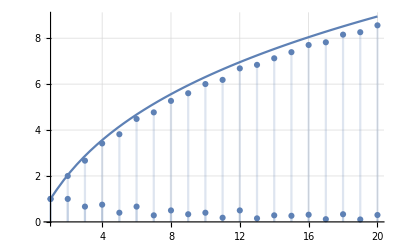

```mathematica
ClearAll[pl]
pl[n_]:=Show[
DiscretePlot[DivisorSigma[0,x]/x,{x,1,n}],
DiscretePlot[Sum[DivisorSigma[0,y]/y,{y,1,x}],{x,1,n}],
Plot[Log[x]^2/2+2 EulerGamma Log[x]+1,{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[20]
```

### Apo 3.3)

```mathematica
ClearAll[f]
f[x_,a_]:=Sum[1/d^a Sum[1/q^a,{q,1,Floor[x/d]}],{d,1,Floor[x]}]
f[3,2]
```

31/18

```mathematica
HoldForm[Sum[DivisorSigma[0,n]/n^α,{n,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[1/d^α Sum[1/q^α,{q,1,Floor[x/d]}],{d,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[1/d^α(1/(1-α)(x^(1-α)d^α)/d+Zeta[α]+O[d^α/x^α]),{d,1,Floor[x]}]]//TraditionalForm
HoldForm[x^(1-α)/(1-α)Sum[1/d,{d,1,Floor[x]}]+Zeta[α]Sum[1/d^α,{d,1,Floor[x]}]+O[Sum[1/x^α,{d,1,Floor[x]}]]]//TraditionalForm
HoldForm[x^(1-α)/(1-α)Sum[1/d,{d,1,Floor[x]}]+Zeta[α]Sum[1/d^α,{d,1,Floor[x]}]+O[x^(1-α)]]//TraditionalForm
HoldForm[x^(1-α)/(1-α)(Log[x]+EulerGamma+O[1/x])+Zeta[α](x^(1-α)/(1-α)+Zeta[α]+O[1/x^α])+O[x^(1-α)]]//TraditionalForm
HoldForm[x^(1-α)/(1-α)Log[x]+x^(1-α)/(1-α)EulerGamma+x^(1-α)/(1-α)O[1/x]+Zeta[α] x^(1-α)/(1-α)+Zeta[α]Zeta[α]+Zeta[α]O[1/x^α]+O[x^(1-α)]]//TraditionalForm
HoldForm[x^(1-α)/(1-α)Log[x]+Zeta[α]^2+x^(1-α)/(1-α)EulerGamma+x^(1-α)/(1-α)O[1/x]+Zeta[α] x^(1-α)/(1-α)+Zeta[α]O[1/x^α]+O[x^(1-α)]]//TraditionalForm
HoldForm[x^(1-α)/(1-α)Log[x]+Zeta[α]^2+O[x^(1-α)]]//TraditionalForm
```

∑_(n=1)^Floor[x] (0n)/n^α

∑_(d=1)^Floor[x] (∑_(q=1)^Floor[x/d] 1/q^α)/d^α

∑_(d=1)^Floor[x] ((x^(1-α) d^α)/((1-α) d)+α+O(d^α/x^α))/d^α

(x^(1-α) ∑_(d=1)^Floor[x] 1/d)/(1-α)+α ∑_(d=1)^Floor[x] 1/d^α+O(∑_(d=1)^Floor[x] 1/x^α)

(x^(1-α) ∑_(d=1)^Floor[x] 1/d)/(1-α)+α ∑_(d=1)^Floor[x] 1/d^α+O(x^(1-α))

(x^(1-α) (log(x)+ℽ+O(1/x)))/(1-α)+α (x^(1-α)/(1-α)+α+O(1/x^α))+O(x^(1-α))

(x^(1-α) log(x))/(1-α)+(x^(1-α) ℽ)/(1-α)+(x^(1-α) O(1/x))/(1-α)+(α x^(1-α))/(1-α)+α α+α O(1/x^α)+O(x^(1-α))

(x^(1-α) log(x))/(1-α)+α^2+(x^(1-α) ℽ)/(1-α)+(x^(1-α) O(1/x))/(1-α)+(α x^(1-α))/(1-α)+α O(1/x^α)+O(x^(1-α))

(x^(1-α) log(x))/(1-α)+α^2+O(x^(1-α))

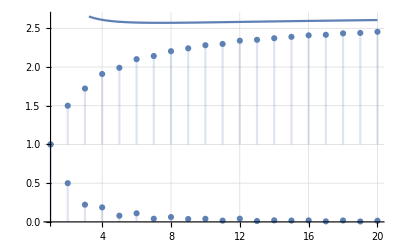

```mathematica
ClearAll[pl]
pl[n_,a_]:=Show[
DiscretePlot[DivisorSigma[0,x]/x^a,{x,1,n}],
DiscretePlot[Sum[DivisorSigma[0,y]/y^a,{y,1,x}],{x,1,n}],
Plot[x^(1-a)/(1-a)Log[x]+Zeta[a]^2+x^(1-a),{x ,1,n}],
GridLines->Automatic,PlotRange->All]
pl[20,2]
```

### Apo 3.4 a)

```mathematica
HoldForm[Sum[MoebiusMu[n] Floor[x/n]^2,{n,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[MoebiusMu[n](x/n-FractionalPart[x/n])^2,{n,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[MoebiusMu[n](x/n)^2,{n,1,Floor[x]}]-2Sum[MoebiusMu[n](x/n)FractionalPart[x/n],{n,1,Floor[x]}]+
Sum[MoebiusMu[n] FractionalPart[x/n]^2,{n,1,Floor[x]}]]//TraditionalForm
HoldForm[x^2 Sum[MoebiusMu[n]/n^2,{n,1,Floor[x]}]+O[x Sum[1/n,{n,1,Floor[x]}]]+O[ Sum[1,{n,1,Floor[x]}]]]//TraditionalForm
HoldForm[x^2 Sum[MoebiusMu[n]/n^2,{n,1,Infinity}]-x^2 O[Sum[1/n^2,{n,x,Infinity}]]+O[ x Log[x]]]//TraditionalForm
HoldForm[x^2/Zeta[2]+x^2 O[1/x]+O[ x Log[x]]]//TraditionalForm
HoldForm[x^2/Zeta[2]+O[ x Log[x]]]//TraditionalForm
```

∑_(n=1)^Floor[x] n Floor[x/n]^2

∑_(n=1)^Floor[x] n (x/n-frac(x/n))^2

∑_(n=1)^Floor[x] n (x/n)^2-2 ∑_(n=1)^Floor[x] (n x frac(x/n))/n+∑_(n=1)^Floor[x] n (frac(x/n))^2

x^2 ∑_(n=1)^Floor[x] n/n^2+O(x ∑_(n=1)^Floor[x] 1/n)+O(∑_(n=1)^Floor[x] 1)

x^2 ∑_(n=1)^∞ n/n^2-x^2 O(∑_(n=x)^∞ 1/n^2)+O(x log(x))

x^2/2+x^2 O(1/x)+O(x log(x))

x^2/2+O(x log(x))

### Apo 3.4 b)

```mathematica
HoldForm[Sum[MoebiusMu[n]/n Floor[x/n],{n,1,Floor[x]}]]//TraditionalForm
HoldForm[Sum[MoebiusMu[n]/n(x/n+O[1]),{n,1,Floor[x]}]]//TraditionalForm
HoldForm[x Sum[MoebiusMu[n]/n^2,{n,1,Floor[x]}]+O[Sum[Abs[MoebiusMu[n]]/n,{n,1,Floor[x]}]]]//TraditionalForm
HoldForm[x/Zeta[2]+O[Log[x]]]//TraditionalForm
```

∑_(n=1)^Floor[x] (n Floor[x/n])/n

∑_(n=1)^Floor[x] (n (x/n+O(1)))/n

x ∑_(n=1)^Floor[x] n/n^2+O(∑_(n=1)^Floor[x] Abs[n]/n)

x/2+O(log(x))

### Apo 3.5 a)

```mathematica
ClearAll[t1]
t1[n_]:=1/2 Sum[MoebiusMu[k] Floor[n/k]^2,{k,1,n}]+1/2
t1[10]
```

32

```mathematica
ClearAll[t]
t[n_]:=Sum[EulerPhi[k],{k,1,n}]
t[10]
t[n_]:=Sum[Map[MoebiusMu[#] k/#&,Divisors[k]]//Total,{k,1,n}]
t[10]
t[n_]:=Sum[MoebiusMu[k]q,{k,1,n},{q,1,Floor[n/k]}]
t[10]
t[n_]:=Sum[MoebiusMu[k] 1/2( 1+Floor[n/k])Floor[n/k],{k,1,n}]
t[10]
t[n_]:=Sum[MoebiusMu[k](1/2 Floor[n/k]+1/2 Floor[n/k]^2),{k,1,n}]
t[10]
t[n_]:=1/2 Sum[MoebiusMu[k] Floor[n/k]^2,{k,1,n}]+1/2 Sum[MoebiusMu[k]Floor[n/k],{k,1,n}]
t[10]
t[n_]:=1/2 Sum[MoebiusMu[k] Floor[n/k]^2,{k,1,n}]+1/2
t[10]
```

32

32

32

«4 more identical outputs»

### Apo 3.5 b)

```mathematica
s[n_]:=Sum[EulerPhi[k]/k,{k,1,n}]
s[6]
```

19/5

```mathematica
sf1[6,MoebiusMu[#]/#&]//formatsf1
```

| d1 | d2 | d3 | d4 | T
1 | 1 |  |  |  | 1
2 | 1 | -1/2 |  |  | 1/2
3 | 1 | -1/3 |  |  | 2/3
4 | 1 | -1/2 |  |  | 1/2
5 | 1 | -1/5 |  |  | 4/5
6 | 1 | -1/2 | -1/3 | 1/6 | 1/3
T |  |  |  |  | 19/5

```mathematica
sf2[6,MoebiusMu[#]/#&]//formatsf2
```

| 1
1 | 6
2 | -3/2
3 | -2/3
4 | 0
5 | -1/5
6 | 1/6
T | 19/5

```mathematica
sf3[6,MoebiusMu[#]/#&]//formatsf3
```

| 1 | 2 | 3 | 4 | 5 | 6 | T
1 | 1 | -1/2 | -1/3 |  | -1/5 | 1/6 | 2/15
2 | 1 | -1/2 | -1/3 |  |  |  | 1/6
3 | 1 | -1/2 |  |  |  |  | 1/2
4 | 1 |  |  |  |  |  | 1
5 | 1 |  |  |  |  |  | 1
6 | 1 |  |  |  |  |  | 1
T | 6 | -3/2 | -2/3 | 0 | -1/5 | 1/6 | 19/5

### Apo 3.6

```mathematica
t[n_]:=Sum[EulerPhi[k]/k^2,{k,1,n}]
t[6]
t[n_]:=Sum[Map[MoebiusMu[#] k/# 1/k^2&,Divisors[k]]//Total,{k,1,n}]
t[6]
t[n_]:=Sum[Map[MoebiusMu[#]/# 1/k&,Divisors[k]]//Total,{k,1,n}]
t[6]
t[n_]:=Sum[Map[MoebiusMu[#] 1/(k#)&,Divisors[k]]//Total,{k,1,n}]
t[6]
t[n_]:=Sum[MoebiusMu[k]/k^2 1/q,{k,1,n},{q,1,Floor[n/k]}]
t[6]
t[n_]:=Sum[MoebiusMu[k]/k^2 1/q,{k,1,n},{q,1,Floor[n/k]}]
t[6]
```

3263/1800

3263/1800

3263/1800

«2 more identical outputs»

### Apo 3.7

### Apo 3.8

### Apo 3.9

### Apo 3.10

### Apo 3.11

### Apo 3.12

### Questions about Integer Functions

#### Apo 3.13

#### Apo 3.14

```mathematica
ClearAll[f]
f[x_,y_]:=Floor[x]-Floor[x-y]
f[11.3,0.1]
f[0.5,0.2]
f[0,0.3]
f[-0.5,0.4]
f[-11.3,0.5]
```

0

0

1

0

0

#### Apo 3.15

```mathematica
ClearAll[f]
f[x_]:=Piecewise[{
{{Floor[x],FractionalPart[x],Floor[x]+FractionalPart[x],FractionalPart[x]+FractionalPart[-x]},x>0},
{{Floor[x],FractionalPart[x],Floor[x]+FractionalPart[x],FractionalPart[x]+FractionalPart[-x]},x==0},
{{-Floor[-x]-1,FractionalPart[x],-Floor[-x]+FractionalPart[x],FractionalPart[x]+FractionalPart[-x]},x<1}
}]
f[11.3]
f[0.5]
f[0]
f[-0.5]
f[-11.3]
```

{11,0.3,11.3,0.}

{0,0.5,0.5,0.}

{0,0,0,0}

{-1,-0.5,-0.5,0.}

{-12,-0.3,-11.3,0.}

#### Apo 3.16

```mathematica
ClearAll[f]
f[x_]:=Floor[2x]-2Floor[x]
f[2.1]
f[0.5]
f[3.6]
```

0

1

1

```mathematica
HoldForm[Floor[2x]-2Floor[x]]//TraditionalForm
HoldForm[Floor[2(Floor[x]+FractionalPart[x])]-2Floor[x]]//TraditionalForm
HoldForm[2Floor[x]+Floor[2FractionalPart[x]]-2Floor[x]]//TraditionalForm
HoldForm[Floor[2FractionalPart[x]]]//TraditionalForm
```

Floor[2 x]-2 Floor[x]

Floor[2 (Floor[x]+frac(x))]-2 Floor[x]

2 Floor[x]+Floor[2 frac(x)]-2 Floor[x]

Floor[2 frac(x)]

#### Apo 3.17

#### Apo 3.18

#### Apo 3.19

#### Apo 3.20

#### Apo 3.21

#### Apo 3.22

#### Apo 3.23

#### Apo 3.24

#### Apo 3.25

#### Apo 3.26

4. Distribution of Prime Numbers

## Suppose π(n)=A ; for which m is π(m)=2A

```mathematica
Reduce[x/Log[x]==(2 y)/Log[y],x,Integers]
```

(x|y)∈ℤ&&((ProductLog[-Log[y]/(2 y)]≠0&&y≥2&&x==ⅇ^(-ProductLog[-Log[y]/(2 y)]))||(ProductLog[-1,-Log[y]/(2 y)]≠0&&y≥2&&x==ⅇ^(-ProductLog[-1,-Log[y]/(2 y)])))

```mathematica
ClearAll[f,g]
f[y_]:=ⅇ^(-ProductLog[-1,-Log[y]/(2 y)])
g[x_]:=x/Log[x]
```

```mathematica
f[100.]
2g[100.]
g[237.]
```

237.581

43.4294

43.3426

## Sieve of Erasthostenes

```mathematica
ClearAll[f]
f[n_]:=ArrayPlot[Partition[Table[PrimeQ[k]/.{False->0,True->1},{k,n+1,n+10000}],100]]
```

```mathematica
f[1000000]
```

-Graphics-

```mathematica
Table[PrimePi[10^k],{k,1,9}]
```

{4,25,168,1229,9592,78498,664579,5761455,50847534}

## ChebyshevPsi and ChebyshevTheta

### Definition Psi, Theta

ψ(x) = ∑_n Λ(n)
θ(x) = ∑_p Log(p)

```mathematica
chebyshevPsi[x_]:=Sum[MangoldtLambda[y],{y,x}]
chebyshevTheta[x_]:=Sum[Log[k],{k,Select[Range[x],PrimeQ]}]
chebyshevPsi1[x_]:=Sum[chebyshevTheta[x^(1/m)],{m,1,Log[2,x]}]
```

#### Example

```mathematica
chebyshevPsi[10]
chebyshevTheta[10]+chebyshevTheta[3]+chebyshevTheta[2]
```

3 Log[2]+2 Log[3]+Log[5]+Log[7]

3 Log[2]+2 Log[3]+Log[5]+Log[7]

```mathematica
Table[{x,chebyshevPsi[x],chebyshevPsi1[x]},{x,10}]//tf
```

1 | 0 | 0
2 | Log[2] | Log[2]
3 | Log[2]+Log[3] | Log[2]+Log[3]
4 | 2 Log[2]+Log[3] | 2 Log[2]+Log[3]
5 | 2 Log[2]+Log[3]+Log[5] | 2 Log[2]+Log[3]+Log[5]
6 | 2 Log[2]+Log[3]+Log[5] | 2 Log[2]+Log[3]+Log[5]
7 | 2 Log[2]+Log[3]+Log[5]+Log[7] | 2 Log[2]+Log[3]+Log[5]+Log[7]
8 | 3 Log[2]+Log[3]+Log[5]+Log[7] | 3 Log[2]+Log[3]+Log[5]+Log[7]
9 | 3 Log[2]+2 Log[3]+Log[5]+Log[7] | 3 Log[2]+2 Log[3]+Log[5]+Log[7]
10 | 3 Log[2]+2 Log[3]+Log[5]+Log[7] | 3 Log[2]+2 Log[3]+Log[5]+Log[7]

### Theorem:

0 ⩽(ψ(x))/x-(ϑ(x))/x⩽(Log(x))^2/(2 √x Log(2))

#### Example

```mathematica
Table[{x,chebyshevPsi[x]/x-chebyshevTheta[x]/x//N,Log[x]^2/(2 √x Log[2.])},{x,500000,1500000,500000}]//tf
```

500000 | 0.00159035 | 0.175664
1000000 | 0.00110242 | 0.137682
1500000 | 0.000902378 | 0.119113

#### Proof:

```mathematica
ClearAll[t1,t2,T1,T2];
t1[x_]:=chebyshevPsi[x]-chebyshevTheta[x]
t2[x_]:=Sum[chebyshevTheta[x^(1/m)],{m,2,Log[2,x]}]
T1[x_]:=Log[2,x] √x Log[√x]
T2[x_]:=Log[x]^2/(2 √x Log[2.])
```

```mathematica
t2[1000]//N
T1[1000]/1000//N
T2[1000]//N
```

40.4356

1.08847

1.08847

```mathematica
chebyshevTheta[100000]//N
100000Log[100000.]
```

99685.4

1.15129×10^6

### Theorem:

θ(x) =π(x) Log(x)-∫_2^x (π(t))/t ⅆt

#### Proof:

Let a(n) be the characteristic function of the primes.
Then ∑_(1<n≤x) a(n)=π(x) , i.e. the prime-counting function.
Then θ(x) = ∑_(p≤x) Log(p) = ∑_(1<n≤x) a(n)Log(n) .
Finally, by applying Abel Summation:
θ(x) =π(x) Log(x)-∫_2^x (π(t))/t ⅆt.

### Theorem:

π(x) =(θ(x))/(Log(x))+∫_2^x (θ(t))/(t (Log(t))^2)ⅆt

#### Proof:

TBD:
Finally, by applying Abel Summation:
π(x) =(θ(x))/(Log(x))+∫_2^x (θ(t))/(t (Log(t))^2)ⅆt.

## Equivalent forms of the PNT

## Inequalities for π(n) and p_n

## Shapiro’s Tauberian Theorem

### Theorem: If ∑_(n⩽x) a(n)⌊x/n⌋=x Log(x)+O(x) Then a) ∑_(n⩽x) (a(n))/n=Log(x)+O(1) b) ∑_(n⩽x) a(n)⩽B x , for a constant B c) ∑_(n⩽x) a(n)⩾A x , for a constant A, x_o

#### Proof:

#### Example:

## Applications of Shapiro’s Theorem

## An asymptotic formula for the partial sums ∑p≤x (1/p)

### Theorem: ∑_(p⩽x) 1/p= Log(Log(x))+A+O(1/(Log(x)))

## The partial sums of the Möbius Function

## Brief sketch of an elementary proof of the Prime Number Theorem

## Exercises

### Apo 4.1

### Apo 4.2

```mathematica
Map[PrimeQ[#]||#==1&,Table[Mod[Prime[x],6],{x,169,279}]]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
PrimeQ[113]
```

True

```mathematica
Prime[172]
```

1021

```mathematica
FactorInteger[187]
```

{{11,1},{17,1}}

### Apo 4.3

```mathematica
Table[{x,x^2+x+41,PrimeQ[x^2+x+41]},{x,0,40}]//tf
```

0 | 41 | True
1 | 43 | True
2 | 47 | True
3 | 53 | True
4 | 61 | True
5 | 71 | True
6 | 83 | True
7 | 97 | True
8 | 113 | True
9 | 131 | True
10 | 151 | True
11 | 173 | True
12 | 197 | True
13 | 223 | True
14 | 251 | True
15 | 281 | True
16 | 313 | True
17 | 347 | True
18 | 383 | True
19 | 421 | True
20 | 461 | True
21 | 503 | True
22 | 547 | True
23 | 593 | True
24 | 641 | True
25 | 691 | True
26 | 743 | True
27 | 797 | True
28 | 853 | True
29 | 911 | True
30 | 971 | True
31 | 1033 | True
32 | 1097 | True
33 | 1163 | True
34 | 1231 | True
35 | 1301 | True
36 | 1373 | True
37 | 1447 | True
38 | 1523 | True
39 | 1601 | True
40 | 1681 | False

```mathematica
Table[Prime[x],{x,26,46}]//tf
```

101
103
107
109
113
127
131
137
139
149
151
157
163
167
173
179
181
191
193
197
199

5. Congruences

## Congruences

## Residue systems

## Linear Congruences

## Reduced residue systems and the Euler—Fermat theorem

## Polynomial congruences modulo p. Lagrange’s theorem

11. Dirichlet Series and Euler Products

## Standard Dirichlet Series

12. The functions ζ(s) and L(s,𝒳)

## *Preliminary Notes

### Definitions

```mathematica
ClearAll[z1,ω,z2,z3]
z1[s_]:=π^(-s/2)Gamma[s/2]Zeta[s]
ω[x_]:=Sum[ⅇ^(-π n^2 x),{n,1,Infinity}]
ω[1+I];
z2[s_]:=Integrate[ω[x](x^(s/2)+x^((1-s)/2))1/x,{x,1,Infinity}]-1/(s(1-s))
z3[s_]:=Integrate[Sum[ⅇ^(-π n^2 x),{n,1,Infinity}](x^(s/2)+x^((1-s)/2))1/x,{x,1,Infinity}]-1/(s(1-s))
z1[4]//N
z3[4]//N
```

0.109662

0.109662

#### Example

#### Application

*Notes; R&D

## Inverse function of (I+ν)(n)

#### General Inverse of an Arithmetic Function

```mathematica
ClearAll[f,g,fg]
f[n_]:=PrimeNu[n]+Floor[1/n];
g[1]=1;
g[n_]:=g[n]=-1/f[1](Apply[Plus,Map[f[n/#]g[#]&,Most[Divisors[n]]]])
fg[n_]:=DivisorSum[n,f[#]g[n/#]&]
Table[{k,f[k]},{k,1,10}]//tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 2
7 | 1
8 | 1
9 | 1
10 | 2

#### Prime Signature “Visitor” Example

```mathematica
parToNum[ls_]:=Apply[Times,MapIndexed[Prime[#2[[1]]]^#1&,ls]]
Table[Map[{#,g[parToNum[#]]}&,IntegerPartitions[k]],{k,0,5}]//tf
```

1 |  |  |  |  |  | 
1
-1 |  |  |  |  |  | 
2
0 | 1 | 1
0 |  |  |  |  |  | 
3
0 | 2 | 1
1 |  | 1 | 1 | 1
3 |  |  |  |  |  | 
4
0 | 3 | 1
0 |  | 2 | 2
0 |  | 2 | 1 | 1
-1 |  |  | 1 | 1 | 1 | 1
-4 |  |  |  |  | 
5
0 | 4 | 1
0 |  | 3 | 2
-1 |  | 3 | 1 | 1
-2 |  |  | 2 | 2 | 1
-5 |  |  | 2 | 1 | 1 | 1
-11 |  |  |  | 1 | 1 | 1 | 1 | 1
-25 |  |  |  |

#### Ideas...??? ( who knows )

```mathematica
CoefficientList[Series[1/(1+x Exp[x]),{x,0,8}],x] Range[0,8]!
```

{1,-1,0,3,-4,-25,114,287,-4152}

```mathematica
h[n_]:=Sum[(-1)^k k!k^(n-k)Binomial[n,k],{k,0,n}]
h[6]
```

114

Hypothesis: If k>=12 Then g[n]=0.

```mathematica
Table[{k,g[2^k 3^2 5^2 7^2 11^2 13^2]},{k,1,14}]//tf
```

1 | -6216
2 | -121308
3 | 186734
4 | 595680
5 | -714360
6 | -1178820
7 | 806130
8 | 1159200
9 | -163800
10 | -453600
11 | -113400
12 | 0
13 | 0
14 | 0

## Is there a formula for the inverse of nFaulhaber_k?

```mathematica
Table[{k, nFaulhaber[1,k],nDirichletInverse[nFaulhaber[1,#]&][k]},{k,1,12}]//tf
```

1 | 1 | 1
2 | 3 | -3
3 | 6 | -6
4 | 10 | -1
5 | 15 | -15
6 | 21 | 15
7 | 28 | -28
8 | 36 | -3
9 | 45 | -9
10 | 55 | 35
11 | 66 | -66
12 | 78 | 6

```mathematica
nEulerPhi[2,6]
```

26

```mathematica
nDirichletProduct[nJordanTotient[2,#]&,1&][5]
Sum[nJordanTotient[2,i]Floor[5/i],{i,1,5}]
nFaulhaber[2,5]
```

25

55

55

```mathematica
f[n_]:=Sum[nJordanTotient[2,i]Floor[n/i],{i,1,n}]
nDirichletProduct[f[#]&,MoebiusMu[#]#^2&][6]
```

26

```mathematica
f[8]
nFaulhaber[2,8]
```

204

204

```mathematica
Table[{2^k, nJordanTotient[3,2^k]},{k,1,6}]//tf
Table[{3^k, nJordanTotient[2,3^k]},{k,1,6}]//tf
Table[{5^k, nJordanTotient[2,5^k]},{k,1,6}]//tf
(3/4) 64^2
```

2 | 7
4 | 56
8 | 448
16 | 3584
32 | 28672
64 | 229376

3 | 8
9 | 72
27 | 648
81 | 5832
243 | 52488
729 | 472392

5 | 24
25 | 600
125 | 15000
625 | 375000
3125 | 9375000
15625 | 234375000

3072

```mathematica
FindGeneratingFunction[{7,56,448,3584,28672},x]
```

-7/(-1+8 x)

```mathematica
nJordanTotient[2,100]
Series[3/(1-4x),{x,0,10}]//Normal
Series[24/(1-25x),{x,0,10}]//Normal
```

7200

3+12 x+48 x^2+192 x^3+768 x^4+3072 x^5+12288 x^6+49152 x^7+196608 x^8+786432 x^9+3145728 x^10

24+600 x+15000 x^2+375000 x^3+9375000 x^4+234375000 x^5+5859375000 x^6+146484375000 x^7+3662109375000 x^8+91552734375000 x^9+2288818359375000 x^10

## Find a function which is 1 if n is 3rd-power free and 0 otherwise

```mathematica
ClearAll[f,g,h]
f[n_]:=DirichletConvolve[Abs[MoebiusMu[k]],Abs[MoebiusMu[k]],k,n]+Floor[1/n]-Abs[MoebiusMu[n]]
g[n_]:=Floor[1/Ceiling[1/(f[n]+1/2)]]

h[n_]:=Floor[Ceiling[(DirichletConvolve[Abs[MoebiusMu[k]],Abs[MoebiusMu[k]],k,n]+Floor[1/n]-Abs[MoebiusMu[n]]+1/2)^-1]^-1]

Table[{n,f[n],g[n],h[n]},{n,1,16}]//tf
```

1 | 1 | 1 | 1
2 | 1 | 1 | 1
3 | 1 | 1 | 1
4 | 1 | 1 | 1
5 | 1 | 1 | 1
6 | 3 | 1 | 1
7 | 1 | 1 | 1
8 | 0 | 0 | 0
9 | 1 | 1 | 1
10 | 3 | 1 | 1
11 | 1 | 1 | 1
12 | 2 | 1 | 1
13 | 1 | 1 | 1
14 | 3 | 1 | 1
15 | 3 | 1 | 1
16 | 0 | 0 | 0

```mathematica
ClearAll[f,g,h,gh]
f[n_]:=nEulerPhi[2,n]
f[n_]:=Floor[Ceiling[(DirichletConvolve[Abs[MoebiusMu[k]],Abs[MoebiusMu[k]],k,n]+Floor[1/n]-Abs[MoebiusMu[n]]+1/2)^-1]^-1]
g[n_]:=nMultiplicativeComponent[f][n]
h[n_]:=nAntiMultiplicativeComponent[f][n]
gh[n_]:=nDirichletProduct[g,h][n]
Table[{k,f[k],g[k],h[k],gh[k]},{k,1,12}]//tf
```

1 | 1 | 1 | 1 | 1
2 | 1 | 1 | 0 | 1
3 | 1 | 1 | 0 | 1
4 | 0 | 0 | Indeterminate | Indeterminate
5 | 1 | 1 | 0 | 1
6 | 1 | 1 | 0 | 1
7 | 1 | 1 | 0 | 1
8 | 0 | 0 | Indeterminate | Indeterminate
9 | 0 | 0 | Indeterminate | Indeterminate
10 | 1 | 1 | 0 | 1
11 | 1 | 1 | 0 | 1
12 | 0 | 0 | Indeterminate | Indeterminate

```mathematica
f[n_]:=Floor[Ceiling[(DirichletConvolve[Abs[MoebiusMu[k]],Abs[MoebiusMu[k]],k,n]+Floor[1/n]-Abs[MoebiusMu[n]]+1/2)^-1]^-1]
nMultiplicativeComponent[f[#]&][1]
nMultiplicativeComponent[f[#]&][3]
nAntiMultiplicativeComponent[f[#]&][1]
nAntiMultiplicativeComponent[f[#]&][3]
```

1

1

1

0

```mathematica
Map[Function[a,nMultiplicativeComponent[f[#]&][a]],Range[36]]
Map[Function[a,nAntiMultiplicativeComponent[f[#]&][a]],Range[36]]
```

{1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,1,1,1,1}

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
DirichletTransform[DirichletConvolve[Abs[MoebiusMu[j]],MoebiusMu[j],j,n],n,s]
```

1/Zeta[2 s]

```mathematica
Table[{3^n,DirichletConvolve[j,MoebiusMu[j],j,3^n]},{n,1,5}]//tf
```

3 | 2
9 | 6
27 | 18
81 | 54
243 | 162

```mathematica
Table[{3^n,nDirichletProduct[#&,MoebiusMu][3^n]},{n,1,5}]//tf
```

3 | 2
9 | 6
27 | 18
81 | 54
243 | 162

```mathematica
DirichletTransform[nDirichletProduct[#&,MoebiusMu][n],n,s]
```

Zeta[-1+s]/Zeta[s]

## Various:

```mathematica
Series[1/(1-z)1/(1-z),{z,0,10}]//Normal
```

1+2 z+3 z^2+4 z^3+5 z^4+6 z^5+7 z^6+8 z^7+9 z^8+10 z^9+11 z^10

```mathematica
f[s_]:=Integrate[t^(s-1)Exp[-t],{t,0,Infinity}]
f[1/2]
```

√π

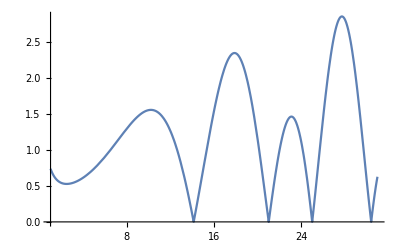

```mathematica
Plot[Abs[DirichletL[1,1,1/2+I  w]],{w,1,31}]
```

```mathematica
ZetaZero[1]//N
ZetaZero[2]//N
ZetaZero[3]//N
ZetaZero[4]//N
```

0.5+14.1347 ⅈ

0.5+21.022 ⅈ

0.5+25.0109 ⅈ

0.5+30.4249 ⅈ

```mathematica
PrimePi[10^5]
```

9592

```mathematica
Select[Partition[Select[Range[10^3],PrimeQ],2,1],#[[2]]-#[[1]]==2&]
```

{{3,5},{5,7},{11,13},{17,19},{29,31},{41,43},{59,61},{71,73},{101,103},{107,109},{137,139},{149,151},{179,181},{191,193},{197,199},{227,229},{239,241},{269,271},{281,283},{311,313},{347,349},{419,421},{431,433},{461,463},{521,523},{569,571},{599,601},{617,619},{641,643},{659,661},{809,811},{821,823},{827,829},{857,859},{881,883}}

```mathematica
Table[{k,PrimePi[10^k],Length[Select[Partition[Select[Range[10^k],PrimeQ],2,1],#[[2]]-#[[1]]==2&]]},{k,1,6}]//tf
```

1 | 4 | 2
2 | 25 | 8
3 | 168 | 35
4 | 1229 | 205
5 | 9592 | 1224
6 | 78498 | 8169

```mathematica
f[n_]:=DirichletConvolve[DirichletConvolve[1,1,j,k],1,k,n]
f[10^9]
Divisors[10^9]//Length
```

3025

100

```mathematica
diriProd[fn_,gn_]:=Function[a,DivisorSum[a,fn[#]gn[a/#]&]]
Fold[diriProd,1&,{1&,1&,1&,1&}][4]
```

15

```mathematica
test[fun_,n_]:=ConstantArray[fun,n]
test[1&,5]
```

{1&,1&,1&,1&,1&}

```mathematica
diriProd2[fun_,n_]:=Fold[diriProd,fun,ConstantArray[fun,n-1]]
diriProd2[1&,4][100]
```

100

```mathematica
diriProd[1&,1&][4]
```

3

```mathematica
nDirichletPower[1&,4][2^5]
```

56

```mathematica
f[s_]:=1/1^s+1/2^s
Solve[f[x]==0]
```

{{x→ConditionalExpression[(ⅈ π)/Log[2]+(2 ⅈ π C[1])/Log[2], C[1]∈ℤ]}}

```mathematica
h[n_]:=nDirichletProduct[MoebiusMu[#]&,#&][n]
Table[{k,h[k]},{k,1,12}]//tf
```

1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
11 | 10
12 | 4

*References / Bibliography

BUGS: nNumberTheory package

## ALERT: DirichletTransform / nDirichletProduct BUG

```mathematica
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
DirichletTransform[nDirichletProduct[DivisorSigma[0,#]&,nDirichletProduct[MoebiusMu,#&][#]&][n],n,s]
```

Zeta[s]^4/Zeta[2 s]

Zeta[s]^3

```mathematica
DirichletTransform[DirichletConvolve[j^2,MoebiusMu[j],j,n],n,s]
DirichletTransform[nDirichletProduct[#^2&,MoebiusMu[#]&][n],n,s]
```

Zeta[-2+s]/Zeta[s]

Zeta[-2+s] Zeta[s]

```mathematica
DirichletConvolve[j^2,MoebiusMu[j],j,12]
nDirichletProduct[#^2&,MoebiusMu[#]&][12]
```

96

96